# Ejercicio I.3: Simulación de elementos de la red

## Nombre del Alumno: Felix Sanz González DNI: 78997168B

# -Graphics-

# 1.- Generacion de paquetes, y transmisiones. Abstracción de un enlace

```mathematica
Clear["Global`*"]
err = 0.1;
npaquetes = 1000;
lambda = 2000;
a = 2;

p = 0.2;
mu = 3000;
TiSW = 1/mu;
TpSW =(a*TiSW-TiSW)/2 
c = 3200000;
l = c/mu//N
```

1/6000

1066.67

```mathematica
RndExp[ratio_] := -Log[RandomReal[]]/ratio//N;
```

```mathematica
RndExp[lambda]
```

0.000118955

```mathematica
GetArrivals[transmisionlista_,tp_]:=Map[(If[#[[4]]==0,#[[1]]+#[[2]]+tp,Unevaluated[Sequence[]]])&,transmisionlista];
```

```mathematica
(*Source[tentrellegadas_,len_,idFlow_,period_,idIn_:0]:=*)
createPackets[lambda_,len_,idFlow_,period_,idIn_]:= 
Module[{checktime =0, n =1, lista = {idIn}},
NestWhileList[({checktime += RndExp[lambda], RndExp[1/l],n,0,0,n++,idFlow,lista,checktime})&, 
{checktime += RndExp[lambda], RndExp[1/l],n,0,0,n++,idFlow,lista,checktime}, (#[[1]]< period)&]];
```

```mathematica
paquetes = createPackets[lambda,l,1,1,0];
paquetes[[1;;5]]
Last[paquetes]
```

{{0.00179726,933.537,1,0,0,1,1,{0},0.00179726},{0.00199113,1956.42,2,0,0,2,1,{0},0.00199113},{0.00492433,120.567,3,0,0,3,1,{0},0.00492433},{0.00517557,2147.2,4,0,0,4,1,{0},0.00517557},{0.00554676,942.033,5,0,0,5,1,{0},0.00554676}}

{1.00039,308.548,2016,0,0,2016,1,{0},1.00039}

```mathematica
(* pkt={chkTime,length,nseqLink,error,nrtx,nseqFlow,flowId,{path},{timePath}} *)

createTx[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
None;
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
]

createTxSW[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
AppendTo[listTx,{checkTime,pck[[2]],n,1,nrtx++,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
];

createTxGBN[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
AppendTo[listTx,{checkTime,pck[[2]],n,1,nrtx++,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c);n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
]
```

```mathematica
paquetesNormales = createTx[paquetes,p,TpSW,c];
```

```mathematica
paquetesNormales⟦1;;5⟧
```

{{0.00179726,933.537,1,0,0,1,1,{0},0.00179726},{0.00242232,1956.42,2,0,0,2,1,{0},0.00199113},{0.00492433,120.567,3,0,0,3,1,{0},0.00492433},{0.00529534,2147.2,4,0,0,4,1,{0},0.00517557},{0.00629968,942.033,5,0,0,5,1,{0},0.00554676}}

```mathematica
paquetesSW = createTxSW[paquetes,p,TpSW,c];
paquetesSW[[1;;5]]
```

{{0.00179726,933.537,1,1,0,1,1,{0},0.00179726},{0.00242232,933.537,1,0,1,1,1,{0},0.00179726},{0.00304738,1956.42,2,0,0,2,1,{0},0.00199113},{0.00492433,120.567,3,1,0,3,1,{0},0.00492433},{0.00529534,120.567,3,1,1,3,1,{0},0.00492433}}

```mathematica
paquetesGBN = createTxGBN[paquetes,p,TpSW,c];
paquetesGBN[[1;;5]]
```

{{0.00179726,933.537,1,0,0,1,1,{0},0.00179726},{0.00208899,1956.42,2,0,0,2,1,{0},0.00199113},{0.00492433,120.567,3,0,0,3,1,{0},0.00492433},{0.00517557,2147.2,4,0,0,4,1,{0},0.00517557},{0.00584657,942.033,5,0,0,5,1,{0},0.00554676}}

```mathematica
Get["C:\\Users\\felix\\Desktop\\Todo\\U.P.V\\MASTER\\Segundo\\Asignaturas\\Rendimiento en Redes de Telecomunicacion\\Casos\\Caso I\\drawTxPRM2024.m"];
```

```mathematica
?drawTxPRM2024`*
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesNormales]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesSW]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
(*Poner 0.005 en WW*)
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesGBN]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
(*Poner 0.004 en WW*)
```

```mathematica
(*Tenemos que conseguir hacer una lista de paquetes que no contenga los paquetes erroneos --> Filtrar *)
(*Esta funcion tambien se encargará de actualizar el tiempo de llegada del paquete*)

filtrarPaquetes[paquetes_,c_,Tp_]:=Map[
(If[#[[4]] == 0,{#[[1]]+#[[2]]/c+Tp, #[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]},Nothing])
&,paquetes]
```

```mathematica
paquetesbuenosNormales = filtrarPaquetes[paquetesNormales,c,TpSW];
paquetesNormales[[1;;20]]
paquetesbuenosNormales[[1;;20]]
paquetesbuenosSW = filtrarPaquetes[paquetesSW,c,TpSW];
paquetesSW[[1;;20]]
paquetesbuenosSW[[1;;20]]
paquetesbuenosGBN = filtrarPaquetes[paquetesGBN,c,TpSW];
paquetesGBN[[1;;20]]
paquetesbuenosGBN[[1;;10]]
```

{{0.00179726,933.537,1,0,0,1,1,{0},0.00179726},{0.00242232,1956.42,2,0,0,2,1,{0},0.00199113},{0.00492433,120.567,3,0,0,3,1,{0},0.00492433},{0.00529534,2147.2,4,0,0,4,1,{0},0.00517557},{0.00629968,942.033,5,0,0,5,1,{0},0.00554676},{0.00692739,22.5174,6,0,0,6,1,{0},0.00604035},{0.00726776,817.708,7,0,0,7,1,{0},0.00605797},{0.00785663,14.6684,8,0,0,8,1,{0},0.00722558},{0.00819455,1097.94,9,0,0,9,1,{0},0.00809254},{0.00887099,724.796,10,0,0,10,1,{0},0.00826619},{0.00943082,6.20003,11,0,0,11,1,{0},0.00828315},{0.00986762,2441.79,12,0,0,12,1,{0},0.00986762},{0.010964,875.14,13,0,0,13,1,{0},0.0098713},{0.0115708,560.682,14,0,0,14,1,{0},0.0102586},{0.0120794,1042.34,15,0,0,15,1,{0},0.010459},{0.0127384,453.49,16,0,0,16,1,{0},0.0111357},{0.0132135,730.755,17,0,0,17,1,{0},0.0116114},{0.0137752,987.249,18,0,0,18,1,{0},0.0118255},{0.014417,135.661,19,0,0,19,1,{0},0.0119525},{0.0147928,886.629,20,0,0,20,1,{0},0.0122877}}

{{0.00225565,933.537,1,0,0,1,1,{0},0.00179726},{0.00320037,1956.42,2,0,0,2,1,{0},0.00199113},{0.00512867,120.567,3,0,0,3,1,{0},0.00492433},{0.00613301,2147.2,4,0,0,4,1,{0},0.00517557},{0.00676073,942.033,5,0,0,5,1,{0},0.00554676},{0.0071011,22.5174,6,0,0,6,1,{0},0.00604035},{0.00768996,817.708,7,0,0,7,1,{0},0.00605797},{0.00802788,14.6684,8,0,0,8,1,{0},0.00722558},{0.00870432,1097.94,9,0,0,9,1,{0},0.00809254},{0.00926415,724.796,10,0,0,10,1,{0},0.00826619},{0.00959942,6.20003,11,0,0,11,1,{0},0.00828315},{0.0107974,2441.79,12,0,0,12,1,{0},0.00986762},{0.0114042,875.14,13,0,0,13,1,{0},0.0098713},{0.0119127,560.682,14,0,0,14,1,{0},0.0102586},{0.0125718,1042.34,15,0,0,15,1,{0},0.010459},{0.0130468,453.49,16,0,0,16,1,{0},0.0111357},{0.0136085,730.755,17,0,0,17,1,{0},0.0116114},{0.0142504,987.249,18,0,0,18,1,{0},0.0118255},{0.0146261,135.661,19,0,0,19,1,{0},0.0119525},{0.0152365,886.629,20,0,0,20,1,{0},0.0122877}}

{{0.00179726,933.537,1,1,0,1,1,{0},0.00179726},{0.00242232,933.537,1,0,1,1,1,{0},0.00179726},{0.00304738,1956.42,2,0,0,2,1,{0},0.00199113},{0.00492433,120.567,3,1,0,3,1,{0},0.00492433},{0.00529534,120.567,3,1,1,3,1,{0},0.00492433},{0.00566635,120.567,3,1,2,3,1,{0},0.00492433},{0.00603736,120.567,3,0,3,3,1,{0},0.00492433},{0.00640837,2147.2,4,0,0,4,1,{0},0.00517557},{0.00741271,942.033,5,0,0,5,1,{0},0.00554676},{0.00804043,22.5174,6,0,0,6,1,{0},0.00604035},{0.0083808,817.708,7,0,0,7,1,{0},0.00605797},{0.00896966,14.6684,8,0,0,8,1,{0},0.00722558},{0.00930758,1097.94,9,0,0,9,1,{0},0.00809254},{0.00998402,724.796,10,0,0,10,1,{0},0.00826619},{0.0105439,6.20003,11,0,0,11,1,{0},0.00828315},{0.0108791,2441.79,12,0,0,12,1,{0},0.00986762},{0.0119755,875.14,13,1,0,13,1,{0},0.0098713},{0.0125823,875.14,13,0,1,13,1,{0},0.0098713},{0.0131891,560.682,14,0,0,14,1,{0},0.0102586},{0.0136977,1042.34,15,1,0,15,1,{0},0.010459}}

{{0.00288072,933.537,1,0,1,1,1,{0},0.00179726},{0.00382543,1956.42,2,0,0,2,1,{0},0.00199113},{0.00624171,120.567,3,0,3,3,1,{0},0.00492433},{0.00724604,2147.2,4,0,0,4,1,{0},0.00517557},{0.00787376,942.033,5,0,0,5,1,{0},0.00554676},{0.00821413,22.5174,6,0,0,6,1,{0},0.00604035},{0.008803,817.708,7,0,0,7,1,{0},0.00605797},{0.00914091,14.6684,8,0,0,8,1,{0},0.00722558},{0.00981735,1097.94,9,0,0,9,1,{0},0.00809254},{0.0103772,724.796,10,0,0,10,1,{0},0.00826619},{0.0107125,6.20003,11,0,0,11,1,{0},0.00828315},{0.0118089,2441.79,12,0,0,12,1,{0},0.00986762},{0.0130225,875.14,13,0,1,13,1,{0},0.0098713},{0.013531,560.682,14,0,0,14,1,{0},0.0102586},{0.0148492,1042.34,15,0,1,15,1,{0},0.010459},{0.0157993,453.49,16,0,1,16,1,{0},0.0111357},{0.0163609,730.755,17,0,0,17,1,{0},0.0116114},{0.0176446,987.249,18,0,1,18,1,{0},0.0118255},{0.0180204,135.661,19,0,0,19,1,{0},0.0119525},{0.0186308,886.629,20,0,0,20,1,{0},0.0122877}}

{{0.00179726,933.537,1,0,0,1,1,{0},0.00179726},{0.00208899,1956.42,2,0,0,2,1,{0},0.00199113},{0.00492433,120.567,3,0,0,3,1,{0},0.00492433},{0.00517557,2147.2,4,0,0,4,1,{0},0.00517557},{0.00584657,942.033,5,0,0,5,1,{0},0.00554676},{0.00614096,22.5174,6,1,0,6,1,{0},0.00604035},{0.00648133,22.5174,6,1,1,6,1,{0},0.00604035},{0.0068217,22.5174,6,1,2,6,1,{0},0.00604035},{0.00716207,22.5174,6,0,3,6,1,{0},0.00604035},{0.00716911,817.708,7,0,0,7,1,{0},0.00605797},{0.00742464,14.6684,8,0,0,8,1,{0},0.00722558},{0.00809254,1097.94,9,0,0,9,1,{0},0.00809254},{0.00843565,724.796,10,1,0,10,1,{0},0.00826619},{0.00899548,724.796,10,1,1,10,1,{0},0.00826619},{0.00955531,724.796,10,1,2,10,1,{0},0.00826619},{0.0101151,724.796,10,0,3,10,1,{0},0.00826619},{0.0103416,6.20003,11,0,0,11,1,{0},0.00828315},{0.0103436,2441.79,12,0,0,12,1,{0},0.00986762},{0.0111066,875.14,13,0,0,13,1,{0},0.0098713},{0.0113801,560.682,14,0,0,14,1,{0},0.0102586}}

{{0.00225565,933.537,1,0,0,1,1,{0},0.00179726},{0.00286703,1956.42,2,0,0,2,1,{0},0.00199113},{0.00512867,120.567,3,0,0,3,1,{0},0.00492433},{0.00601324,2147.2,4,0,0,4,1,{0},0.00517557},{0.00630763,942.033,5,0,0,5,1,{0},0.00554676},{0.00733577,22.5174,6,0,3,6,1,{0},0.00604035},{0.00759131,817.708,7,0,0,7,1,{0},0.00605797},{0.00759589,14.6684,8,0,0,8,1,{0},0.00722558},{0.00860231,1097.94,9,0,0,9,1,{0},0.00809254},{0.0105083,724.796,10,0,3,10,1,{0},0.00826619}}

# 2 y 3.- Abstracción de un nodo de conmutación. Funciones de filtrado y multiplexado de paquetes.

Debemos implementar una función que nos permita eliminar los paquetes que contienen error, segun el campo de paquete que indica si es un paquete con error

```mathematica
(*Esta funcion tambien se encargará de actualizar el tiempo de llegada del paquete*)

filtrarPaquetes[paquetes_,c_,Tp_]:=Map[
(If[#[[4]] == 0,{#[[1]]+#[[2]]/c+Tp, #[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]},Nothing])
&,paquetes]
```

Debemos implementar una función que nos permita dividir y conmutar  el trafico entrante a un nodo por sus distintos enlaces de salida. 
Está función tiene como parámetros de entrada la lista de paquetes, las probabilidades de los enlaces de salida y los enlaces de salida

```mathematica
(*Esta funcion da error y NO SE USA*)
Node1[in_,probs_]:=Module[{cumulativeProbs,outcomes,nProbs,nGroups,r,assignedGroups},(*Verificar que las probabilidades sumen 1*)If[Total[probs]!=1,Return["Error: La suma de las probabilidades debe ser 1."]];
(*Calcular los límites acumulados de las probabilidades*)
cumulativeProbs=Accumulate[probs];
(*Número de probabilidades y número de grupos*)
nProbs=Length[probs];
nGroups=nProbs;
(*Asignar cada elemento de'in' a un grupo según probabilidades acumuladas*)
assignedGroups=Map[With[{r=RandomReal[]},FirstPosition[cumulativeProbs,_?(#>=r&)][[1]],in];
(*Mostrar valores aleatorios y asignaciones para depuración*)
Print["Valores aleatorios: ",r,Length[in]]];
Print["Grupos asignados: ",assignedGroups];
(*Crear la lista de resultados agrupados*)
outcomes=Table[Select[Transpose[{in,assignedGroups}],#[[2]]==i+1&][[All,1]],{i,1,Length[probs]}];
(*Devolver los resultados agrupados por etiquetas*)
outcomes]
```

```mathematica
(* pkt={chkTime,length,nseqFlow,error,nrtx,nseqLink,flowId} *)
(*Esta es la función que se usa*)

Node2[in_,prob_]:=Reap[
Map[
If[RandomReal[]<prob,Sow[#,1],Sow[#,2]]&,in],
_,#2&][[2]];
```

Debemos implementar una función que nos permita multiplexar el trafico entrante a un nodo, para asi obtener una unica lista, ordenada segun el instante de llegada de cada paquete.

```mathematica
(* pkt={chkTime,length,nseqFlow,error,nrtx,nseqLink,flowId,{path} *)
Multiplexar[in_,idNodo_]:=Module[{aux={},aux2={},nodes={},times={}},
aux=Flatten[in,1]; (*Concatenar listas de paquetes en una sola lista*)
aux=SortBy[aux,#[[1]]&]; (*Ordenar la nueva lista en base al tiempo en el que han llegado los paquetes al nodo*)
Map[{

nodes=#[[8]];(*Extraer los nodos por los que ha pasado el paquete actual*)
AppendTo[nodes,idNodo]; (*Agregar el nodo actual a la lista de nodos por los que ha pasado el paquete actual*)

AppendTo[aux2,{#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],nodes,#[[9]]}]}&,aux]; (*Crea la nueva lista de paquetes*)
	aux2
];
```

```mathematica
{enlace1,enlace2}= Node2[paquetesbuenosNormales[[1;;15]],0.5];
Flatten[{enlace1,enlace2},1]
enlace1
enlace2
```

{{0.00225565,933.537,1,0,0,1,1,{0},0.00179726},{0.00320037,1956.42,2,0,0,2,1,{0},0.00199113},{0.00512867,120.567,3,0,0,3,1,{0},0.00492433},{0.00613301,2147.2,4,0,0,4,1,{0},0.00517557},{0.00676073,942.033,5,0,0,5,1,{0},0.00554676},{0.0071011,22.5174,6,0,0,6,1,{0},0.00604035},{0.00768996,817.708,7,0,0,7,1,{0},0.00605797},{0.00802788,14.6684,8,0,0,8,1,{0},0.00722558},{0.00870432,1097.94,9,0,0,9,1,{0},0.00809254},{0.00959942,6.20003,11,0,0,11,1,{0},0.00828315},{0.0114042,875.14,13,0,0,13,1,{0},0.0098713},{0.0119127,560.682,14,0,0,14,1,{0},0.0102586},{0.0125718,1042.34,15,0,0,15,1,{0},0.010459},{0.00926415,724.796,10,0,0,10,1,{0},0.00826619},{0.0107974,2441.79,12,0,0,12,1,{0},0.00986762}}

{{0.00225565,933.537,1,0,0,1,1,{0},0.00179726},{0.00320037,1956.42,2,0,0,2,1,{0},0.00199113},{0.00512867,120.567,3,0,0,3,1,{0},0.00492433},{0.00613301,2147.2,4,0,0,4,1,{0},0.00517557},{0.00676073,942.033,5,0,0,5,1,{0},0.00554676},{0.0071011,22.5174,6,0,0,6,1,{0},0.00604035},{0.00768996,817.708,7,0,0,7,1,{0},0.00605797},{0.00802788,14.6684,8,0,0,8,1,{0},0.00722558},{0.00870432,1097.94,9,0,0,9,1,{0},0.00809254},{0.00959942,6.20003,11,0,0,11,1,{0},0.00828315},{0.0114042,875.14,13,0,0,13,1,{0},0.0098713},{0.0119127,560.682,14,0,0,14,1,{0},0.0102586},{0.0125718,1042.34,15,0,0,15,1,{0},0.010459}}

{{0.00926415,724.796,10,0,0,10,1,{0},0.00826619},{0.0107974,2441.79,12,0,0,12,1,{0},0.00986762}}

```mathematica
in2 = Multiplexar[{enlace1,enlace2},A]
```

{{0.00225565,933.537,1,0,0,1,1,{0,A},0.00179726},{0.00320037,1956.42,2,0,0,2,1,{0,A},0.00199113},{0.00512867,120.567,3,0,0,3,1,{0,A},0.00492433},{0.00613301,2147.2,4,0,0,4,1,{0,A},0.00517557},{0.00676073,942.033,5,0,0,5,1,{0,A},0.00554676},{0.0071011,22.5174,6,0,0,6,1,{0,A},0.00604035},{0.00768996,817.708,7,0,0,7,1,{0,A},0.00605797},{0.00802788,14.6684,8,0,0,8,1,{0,A},0.00722558},{0.00870432,1097.94,9,0,0,9,1,{0,A},0.00809254},{0.00926415,724.796,10,0,0,10,1,{0,A},0.00826619},{0.00959942,6.20003,11,0,0,11,1,{0,A},0.00828315},{0.0107974,2441.79,12,0,0,12,1,{0,A},0.00986762},{0.0114042,875.14,13,0,0,13,1,{0,A},0.0098713},{0.0119127,560.682,14,0,0,14,1,{0,A},0.0102586},{0.0125718,1042.34,15,0,0,15,1,{0,A},0.010459}}

```mathematica
(*Esta funcion permite añadir numeros de secuencia a los paquetes de un flujo, es decir, a los paquetes que ya se sabe que van por un enlace*)
añadirNumSec[lista_,max_]:=Table[Append[lista[[i]],Mod[i-1,max]],{i,1,Length[lista]}]
```

```mathematica
añadirNumSec[enlace1,4]
```

{{0.00225565,933.537,1,0,0,1,1,{0},0.00179726,0},{0.00320037,1956.42,2,0,0,2,1,{0},0.00199113,1},{0.00512867,120.567,3,0,0,3,1,{0},0.00492433,2},{0.00613301,2147.2,4,0,0,4,1,{0},0.00517557,3},{0.00676073,942.033,5,0,0,5,1,{0},0.00554676,0},{0.0071011,22.5174,6,0,0,6,1,{0},0.00604035,1},{0.00768996,817.708,7,0,0,7,1,{0},0.00605797,2},{0.00802788,14.6684,8,0,0,8,1,{0},0.00722558,3},{0.00870432,1097.94,9,0,0,9,1,{0},0.00809254,0},{0.00959942,6.20003,11,0,0,11,1,{0},0.00828315,1},{0.0114042,875.14,13,0,0,13,1,{0},0.0098713,2},{0.0119127,560.682,14,0,0,14,1,{0},0.0102586,3},{0.0125718,1042.34,15,0,0,15,1,{0},0.010459,0}}

# 4A.- Simulación de transmisión de paquetes en la topología de red SIN protocolo

```mathematica
SetAttributes[createPrimitive,HoldAll];
MakeBoxes[Interpretation[expr,p]]//DisplayForm;
InterpretationBox["expr",p]//DisplayForm;
g=Show[Graphics[face[]],Graphics[Translate[face[0.2],{2,0}]]];

createPrimitive[patt_,expr_]:=Typeset`MakeBoxes[p:patt,fmt_,Graphics]:=Typeset`MakeBoxes[Interpretation[expr,p],fmt,Graphics]
arrow=Graphics[face[0.01]];
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4,10->1,6->5,7->2,4->8,3->9},VertexCoordinateRules->{1->{0.5,0},2->{2,1},3->{4,1},4->{4,-1},5->{2,-1},6->{1.5,-1.5},7->{2,1.5},8->{4.5,-1},9->{4.5,1},10->{0,0}},VertexRenderingFunction->(If[#2≤5,{EdgeForm[Black],Cyan,Disk[#1,0.15],Black,Text[#2,#1]}]&),EdgeRenderingFunction-> (If[#2[[1]]≤5&&#2[[2]]≤5,{{Arrowheads[{0,.03,0,.03,.03}],Arrow[#1]},Inset[arrow,Mean[#1],Automatic,0.5,#[[2]]-#[[1]],Background->White]},{Arrowheads[{0,.03,.03}],Arrow[#1]}]&)
]
```

-Graphics-

```mathematica
npaquetes = 250;
err = 0.1;
lambda = 2000;
a = 2;
period = 1;

p = 0.05;
mu = 3000;
TiSW = 1/mu;
TpSW =(a*TiSW-TiSW)/2 
c = 3200000;
l = c/mu//N
prob1 = 1/4;
prob2 = 1/3;
prob5 = 1/2;
```

1/6000

1066.67

```mathematica
in1 = createPackets[lambda,l,1,period,"Ori-1"];
Last[in1]
in5 = createPackets[lambda,l,1,period,"Ori-5"];
Last[in5]
in2 = createPackets[lambda,l,1,period,"Ori-2"];
Last[in2]
in1[[1;;15]];
totalin = Length[in1]+Length[in5]+Length[in2]
```

{1.00036,726.214,2035,0,0,2035,1,{Ori-1},1.00036}

{1.0005,178.321,2012,0,0,2012,1,{Ori-5},1.0005}

{1.00014,421.068,1974,0,0,1974,1,{Ori-2},1.00014}

6021

```mathematica
{paquetes12,paquetes15} =Node2[in1,prob1];

paquetes12[[1;;15]]
paquetes15[[1;;15]]
Length[paquetes12];
Length[paquetes15];
Length[paquetes12]/(Length[paquetes15]+Length[paquetes12])//N
```

{{0.000648199,422.436,1,0,0,1,1,{Ori-1},0.000648199},{0.00138303,2560.07,3,0,0,3,1,{Ori-1},0.00138303},{0.00570151,143.571,11,0,0,11,1,{Ori-1},0.00570151},{0.00602406,1207.63,12,0,0,12,1,{Ori-1},0.00602406},{0.00630845,1746.62,13,0,0,13,1,{Ori-1},0.00630845},{0.00887927,479.868,22,0,0,22,1,{Ori-1},0.00887927},{0.0123432,951.349,26,0,0,26,1,{Ori-1},0.0123432},{0.016433,457.869,31,0,0,31,1,{Ori-1},0.016433},{0.016734,470.244,34,0,0,34,1,{Ori-1},0.016734},{0.0171744,90.7546,35,0,0,35,1,{Ori-1},0.0171744},{0.0174673,263.267,37,0,0,37,1,{Ori-1},0.0174673},{0.0206775,1829.39,41,0,0,41,1,{Ori-1},0.0206775},{0.0217613,102.911,44,0,0,44,1,{Ori-1},0.0217613},{0.021956,3011.93,45,0,0,45,1,{Ori-1},0.021956},{0.0226664,2339.83,46,0,0,46,1,{Ori-1},0.0226664}}

{{0.00079127,920.674,2,0,0,2,1,{Ori-1},0.00079127},{0.00208329,227.922,4,0,0,4,1,{Ori-1},0.00208329},{0.00226136,1105.99,5,0,0,5,1,{Ori-1},0.00226136},{0.0032151,5550.86,6,0,0,6,1,{Ori-1},0.0032151},{0.00337058,381.397,7,0,0,7,1,{Ori-1},0.00337058},{0.00366409,837.991,8,0,0,8,1,{Ori-1},0.00366409},{0.00448963,10.9285,9,0,0,9,1,{Ori-1},0.00448963},{0.00532174,192.987,10,0,0,10,1,{Ori-1},0.00532174},{0.00674352,1571.16,14,0,0,14,1,{Ori-1},0.00674352},{0.00677745,247.332,15,0,0,15,1,{Ori-1},0.00677745},{0.00694049,1429.85,16,0,0,16,1,{Ori-1},0.00694049},{0.00728803,3279.41,17,0,0,17,1,{Ori-1},0.00728803},{0.00766726,1335.59,18,0,0,18,1,{Ori-1},0.00766726},{0.00808487,1599.93,19,0,0,19,1,{Ori-1},0.00808487},{0.00836792,2718.17,20,0,0,20,1,{Ori-1},0.00836792}}

0.255037

```mathematica
tx12 = createTx[paquetes12,p,TpSW,c];
tx15 = createTx[paquetes15,p,TpSW,c];
```

```mathematica
tx15[[1;;10]]
in5[[1;;10]]

inOKtx15 = filtrarPaquetes[tx15,c,TpSW];

intotal5= Multiplexar[{in5,inOKtx15},5];
intotal5[[1;;10]]

{paquetes52,paquetes54} = Node2[intotal5,prob5];
tx52 = createTx[paquetes52,p,TpSW,c];
tx54 = createTx[paquetes54,p,TpSW,c];
```

{{0.00079127,920.674,1,0,0,2,1,{Ori-1},0.00079127},{0.00208329,227.922,2,0,0,4,1,{Ori-1},0.00208329},{0.00248785,1105.99,3,0,0,5,1,{Ori-1},0.00226136},{0.0032151,5550.86,4,0,0,6,1,{Ori-1},0.0032151},{0.00528308,381.397,5,0,0,7,1,{Ori-1},0.00337058},{0.0057356,837.991,6,0,0,8,1,{Ori-1},0.00366409},{0.0063308,10.9285,7,0,0,9,1,{Ori-1},0.00448963},{0.00666755,192.987,8,0,0,10,1,{Ori-1},0.00532174},{0.00706119,1571.16,9,0,0,14,1,{Ori-1},0.00674352},{0.00788551,247.332,10,0,0,15,1,{Ori-1},0.00677745}}

{{0.000273814,595.356,1,0,0,1,1,{Ori-5},0.000273814},{0.000620522,971.727,2,0,0,2,1,{Ori-5},0.000620522},{0.00136984,644.289,3,0,0,3,1,{Ori-5},0.00136984},{0.00142362,3583.83,4,0,0,4,1,{Ori-5},0.00142362},{0.0018518,482.581,5,0,0,5,1,{Ori-5},0.0018518},{0.00254302,1405.61,6,0,0,6,1,{Ori-5},0.00254302},{0.00260141,1271.79,7,0,0,7,1,{Ori-5},0.00260141},{0.00283077,56.4332,8,0,0,8,1,{Ori-5},0.00283077},{0.00469177,116.912,9,0,0,9,1,{Ori-5},0.00469177},{0.00548888,2248.69,10,0,0,10,1,{Ori-5},0.00548888}}

{{0.000273814,595.356,1,0,0,1,1,{Ori-5,5},0.000273814},{0.000620522,971.727,2,0,0,2,1,{Ori-5,5},0.000620522},{0.00124565,920.674,1,0,0,2,1,{Ori-1,5},0.00079127},{0.00136984,644.289,3,0,0,3,1,{Ori-5,5},0.00136984},{0.00142362,3583.83,4,0,0,4,1,{Ori-5,5},0.00142362},{0.0018518,482.581,5,0,0,5,1,{Ori-5,5},0.0018518},{0.00232118,227.922,2,0,0,4,1,{Ori-1,5},0.00208329},{0.00254302,1405.61,6,0,0,6,1,{Ori-5,5},0.00254302},{0.00260141,1271.79,7,0,0,7,1,{Ori-5,5},0.00260141},{0.00283077,56.4332,8,0,0,8,1,{Ori-5,5},0.00283077}}

```mathematica
inOKtx12 = filtrarPaquetes[tx12,c,TpSW];
inOKtx52 = filtrarPaquetes[tx52,c,TpSW];
intotal2 = Multiplexar[{in2,inOKtx52, inOKtx12},2];
in2[[1;;10]]
inOKtx52[[1;;10]]
inOKtx12[[1;;10]]
intotal2[[1;;10]]
```

{{0.000117943,1330.66,1,0,0,1,1,{Ori-2},0.000117943},{0.00208773,74.0278,2,0,0,2,1,{Ori-2},0.00208773},{0.00338115,513.213,3,0,0,3,1,{Ori-2},0.00338115},{0.00411533,1053.09,4,0,0,4,1,{Ori-2},0.00411533},{0.00542177,2562.54,5,0,0,5,1,{Ori-2},0.00542177},{0.00564301,214.424,6,0,0,6,1,{Ori-2},0.00564301},{0.00638805,494.398,7,0,0,7,1,{Ori-2},0.00638805},{0.0066277,1059.08,8,0,0,8,1,{Ori-2},0.0066277},{0.00702821,206.713,9,0,0,9,1,{Ori-2},0.00702821},{0.00727637,94.3959,10,0,0,10,1,{Ori-2},0.00727637}}

{{0.000626529,595.356,1,0,0,1,1,{Ori-5,5},0.000273814},{0.00170002,920.674,2,0,0,2,1,{Ori-1,5},0.00079127},{0.0022347,644.289,3,0,0,3,1,{Ori-5,5},0.00136984},{0.00316551,1271.79,4,0,0,7,1,{Ori-5,5},0.00260141},{0.00384447,1105.99,5,0,0,5,1,{Ori-1,5},0.00226136},{0.00576991,160.609,6,0,0,11,1,{Ori-5,5},0.00555305},{0.00631356,673.016,7,0,0,12,1,{Ori-5,5},0.0057192},{0.00690876,837.991,8,0,0,8,1,{Ori-1,5},0.00366409},{0.00756176,878.538,9,0,0,16,1,{Ori-5,5},0.00712055},{0.00812895,748.331,10,0,0,18,1,{Ori-5,5},0.00747059}}

{{0.000946877,422.436,1,0,0,1,1,{Ori-1},0.000648199},{0.00234972,2560.07,2,0,0,3,1,{Ori-1},0.00138303},{0.00591304,143.571,3,0,0,11,1,{Ori-1},0.00570151},{0.00662376,1207.63,4,0,0,12,1,{Ori-1},0.00602406},{0.00750291,1746.62,5,0,0,13,1,{Ori-1},0.00630845},{0.0091959,479.868,6,0,0,22,1,{Ori-1},0.00887927},{0.0128072,951.349,7,0,0,26,1,{Ori-1},0.0123432},{0.0167428,457.869,8,0,0,31,1,{Ori-1},0.016433},{0.017223,470.244,9,0,0,34,1,{Ori-1},0.016734},{0.0175847,90.7546,10,0,0,35,1,{Ori-1},0.0171744}}

{{0.000117943,1330.66,1,0,0,1,1,{Ori-2,2},0.000117943},{0.000626529,595.356,1,0,0,1,1,{Ori-5,5,2},0.000273814},{0.000946877,422.436,1,0,0,1,1,{Ori-1,2},0.000648199},{0.00170002,920.674,2,0,0,2,1,{Ori-1,5,2},0.00079127},{0.00208773,74.0278,2,0,0,2,1,{Ori-2,2},0.00208773},{0.0022347,644.289,3,0,0,3,1,{Ori-5,5,2},0.00136984},{0.00234972,2560.07,2,0,0,3,1,{Ori-1,2},0.00138303},{0.00316551,1271.79,4,0,0,7,1,{Ori-5,5,2},0.00260141},{0.00338115,513.213,3,0,0,3,1,{Ori-2,2},0.00338115},{0.00384447,1105.99,5,0,0,5,1,{Ori-1,5,2},0.00226136}}

```mathematica
{paquetes23,paquetes24} = Node2[intotal2,prob2];

tx23 = createTx[paquetes23,p,TpSW,c];
tx24 = createTx[paquetes24,p,TpSW,c];
```

```mathematica
inOK3 = filtrarPaquetes[tx23,c,TpSW];
out3 = Multiplexar[{inOK3},3];
out3[[1;;10]]
```

{{0.000700442,1330.66,1,0,0,1,1,{Ori-2,2,3},0.000117943},{0.00121982,595.356,2,0,0,1,1,{Ori-5,5,2,3},0.000273814},{0.00168517,422.436,3,0,0,1,1,{Ori-1,2,3},0.000648199},{0.00260271,644.289,4,0,0,3,1,{Ori-5,5,2,3},0.00136984},{0.00373606,2560.07,5,0,0,3,1,{Ori-1,2,3},0.00138303},{0.00441502,1105.99,6,0,0,5,1,{Ori-1,5,2,3},0.00226136},{0.00507744,1053.09,7,0,0,4,1,{Ori-2,2,3},0.00411533},{0.00638923,2562.54,8,0,0,5,1,{Ori-2,2,3},0.00542177},{0.00677275,160.609,9,0,0,11,1,{Ori-5,5,2,3},0.00555305},{0.00715095,143.571,10,0,0,11,1,{Ori-1,2,3},0.00570151}}

```mathematica
inOKtx54 = filtrarPaquetes[tx54,c,TpSW];
inOKtx24 = filtrarPaquetes[tx24,c,TpSW];
intotal4 = Multiplexar[{inOKtx54, inOKtx24},4];
inOKtx54[[1;;10]]
inOKtx24[[1;;10]]
intotal4[[1;;10]]
```

{{0.00109085,971.727,1,0,0,2,1,{Ori-5,5},0.000620522},{0.00271024,3583.83,2,0,0,4,1,{Ori-5,5},0.00142362},{0.00319438,482.581,3,0,0,5,1,{Ori-5,5},0.0018518},{0.00359894,227.922,4,0,0,4,1,{Ori-1,5},0.00208329},{0.00437152,1405.61,5,0,0,6,1,{Ori-5,5},0.00254302},{0.00472249,56.4332,6,0,0,8,1,{Ori-5,5},0.00283077},{0.00509236,116.912,7,0,0,9,1,{Ori-5,5},0.00469177},{0.00716034,5550.86,8,0,0,6,1,{Ori-1,5},0.0032151},{0.00819638,2248.69,9,0,0,10,1,{Ori-5,5},0.00548888},{0.0086489,381.397,10,0,0,7,1,{Ori-1,5},0.00337058}}

{{0.0021544,920.674,1,0,0,2,1,{Ori-1,5,2},0.00079127},{0.00251087,74.0278,2,0,0,2,1,{Ori-2,2},0.00208773},{0.00372961,1271.79,3,0,0,7,1,{Ori-5,5,2},0.00260141},{0.00422332,513.213,4,0,0,3,1,{Ori-2,2},0.00338115},{0.00587668,214.424,5,0,0,6,1,{Ori-2,2},0.00564301},{0.00716781,1207.63,6,0,0,12,1,{Ori-1,2},0.00602406},{0.0082154,1746.62,7,0,0,13,1,{Ori-1,2},0.00630845},{0.00881399,848.817,8,0,0,11,1,{Ori-2,2},0.00819061},{0.00960785,247.332,9,0,0,15,1,{Ori-1,5,2},0.00677745},{0.0103169,202.022,10,0,0,17,1,{Ori-2,2},0.0100871}}

{{0.00109085,971.727,1,0,0,2,1,{Ori-5,5,4},0.000620522},{0.0021544,920.674,1,0,0,2,1,{Ori-1,5,2,4},0.00079127},{0.00251087,74.0278,2,0,0,2,1,{Ori-2,2,4},0.00208773},{0.00271024,3583.83,2,0,0,4,1,{Ori-5,5,4},0.00142362},{0.00319438,482.581,3,0,0,5,1,{Ori-5,5,4},0.0018518},{0.00359894,227.922,4,0,0,4,1,{Ori-1,5,4},0.00208329},{0.00372961,1271.79,3,0,0,7,1,{Ori-5,5,2,4},0.00260141},{0.00422332,513.213,4,0,0,3,1,{Ori-2,2,4},0.00338115},{0.00437152,1405.61,5,0,0,6,1,{Ori-5,5,4},0.00254302},{0.00472249,56.4332,6,0,0,8,1,{Ori-5,5,4},0.00283077}}

```mathematica
out4 = intotal4;
out4[[1;;10]]
```

{{0.00109085,971.727,1,0,0,2,1,{Ori-5,5,4},0.000620522},{0.0021544,920.674,1,0,0,2,1,{Ori-1,5,2,4},0.00079127},{0.00251087,74.0278,2,0,0,2,1,{Ori-2,2,4},0.00208773},{0.00271024,3583.83,2,0,0,4,1,{Ori-5,5,4},0.00142362},{0.00319438,482.581,3,0,0,5,1,{Ori-5,5,4},0.0018518},{0.00359894,227.922,4,0,0,4,1,{Ori-1,5,4},0.00208329},{0.00372961,1271.79,3,0,0,7,1,{Ori-5,5,2,4},0.00260141},{0.00422332,513.213,4,0,0,3,1,{Ori-2,2,4},0.00338115},{0.00437152,1405.61,5,0,0,6,1,{Ori-5,5,4},0.00254302},{0.00472249,56.4332,6,0,0,8,1,{Ori-5,5,4},0.00283077}}

```mathematica
totalout = Length[out3]+Length[out4]
```

6021

# 5A.- Simulación de transmisión de paquetes en la topología de red CON protocolo S&W:

```mathematica
in1SW = createPackets[lambda,l,1,period,"Ori-1"];
in5SW = createPackets[lambda,l,1,period,"Ori-5"];
in2SW = createPackets[lambda,l,1,period,"Ori-2"];
in1SW[[1;;15]];
totalinSW = Length[in1SW]+Length[in5SW]+Length[in2SW]
```

5998

```mathematica
{paquetes12SW,paquetes15SW} =Node2[in1SW,prob1];

paquetes12SW[[1;;15]]
paquetes15SW[[1;;15]]
Length[paquetes12SW];
Length[paquetes15SW];
Length[paquetes12SW]/(Length[paquetes15SW]+Length[paquetes12SW])//N
```

{{0.00182161,1633.72,1,0,0,1,1,{Ori-1},0.00182161},{0.00237482,807.596,2,0,0,2,1,{Ori-1},0.00237482},{0.00407468,1049.35,3,0,0,3,1,{Ori-1},0.00407468},{0.00527162,136.789,4,0,0,4,1,{Ori-1},0.00527162},{0.00530381,125.981,5,0,0,5,1,{Ori-1},0.00530381},{0.00578377,897.661,6,0,0,6,1,{Ori-1},0.00578377},{0.00693791,3851.31,7,0,0,7,1,{Ori-1},0.00693791},{0.00762654,911.763,8,0,0,8,1,{Ori-1},0.00762654},{0.00794124,276.608,9,0,0,9,1,{Ori-1},0.00794124},{0.00799587,1314.25,10,0,0,10,1,{Ori-1},0.00799587},{0.00841137,524.846,11,0,0,11,1,{Ori-1},0.00841137},{0.00870248,2832.57,12,0,0,12,1,{Ori-1},0.00870248},{0.00939076,1674.64,14,0,0,14,1,{Ori-1},0.00939076},{0.0100801,170.927,16,0,0,16,1,{Ori-1},0.0100801},{0.0107543,347.594,17,0,0,17,1,{Ori-1},0.0107543}}

{{0.00916756,46.4795,13,0,0,13,1,{Ori-1},0.00916756},{0.00993692,2611.15,15,0,0,15,1,{Ori-1},0.00993692},{0.0158653,1728.48,25,0,0,25,1,{Ori-1},0.0158653},{0.0178378,623.689,28,0,0,28,1,{Ori-1},0.0178378},{0.0196536,100.043,30,0,0,30,1,{Ori-1},0.0196536},{0.0206587,409.296,33,0,0,33,1,{Ori-1},0.0206587},{0.0223358,4896.97,39,0,0,39,1,{Ori-1},0.0223358},{0.0245898,185.106,43,0,0,43,1,{Ori-1},0.0245898},{0.0252532,127.229,44,0,0,44,1,{Ori-1},0.0252532},{0.028642,3172.11,50,0,0,50,1,{Ori-1},0.028642},{0.0337238,61.533,58,0,0,58,1,{Ori-1},0.0337238},{0.0352548,1694.61,63,0,0,63,1,{Ori-1},0.0352548},{0.0383526,467.64,66,0,0,66,1,{Ori-1},0.0383526},{0.0402457,496.518,69,0,0,69,1,{Ori-1},0.0402457},{0.0402916,212.727,71,0,0,71,1,{Ori-1},0.0402916}}

0.756689

```mathematica
tx12SW = createTxSW[paquetes12SW,p,TpSW,c];
tx15SW = createTxSW[paquetes15SW,p,TpSW,c];
```

```mathematica
tx15SW[[1;;10]]
in5SW[[1;;10]]

inOKtx15SW = filtrarPaquetes[tx15SW,c,TpSW];

intotal5SW= Multiplexar[{in5SW,inOKtx15SW},5];
intotal5SW[[1;;10]]

{paquetes52SW,paquetes54SW} = Node2[intotal5SW,prob5];
tx52SW = createTxSW[paquetes52SW,p,TpSW,c];
tx54SW = createTxSW[paquetes54SW,p,TpSW,c];
```

{{0.00916756,46.4795,1,0,0,13,1,{Ori-1},0.00916756},{0.00993692,2611.15,2,0,0,15,1,{Ori-1},0.00993692},{0.0158653,1728.48,3,0,0,25,1,{Ori-1},0.0158653},{0.0178378,623.689,4,0,0,28,1,{Ori-1},0.0178378},{0.0196536,100.043,5,0,0,30,1,{Ori-1},0.0196536},{0.0206587,409.296,6,0,0,33,1,{Ori-1},0.0206587},{0.0223358,4896.97,7,0,0,39,1,{Ori-1},0.0223358},{0.0245898,185.106,8,0,0,43,1,{Ori-1},0.0245898},{0.0252532,127.229,9,1,0,44,1,{Ori-1},0.0252532},{0.0256263,127.229,9,0,1,44,1,{Ori-1},0.0252532}}

{{0.000193961,1584.94,1,0,0,1,1,{Ori-5},0.000193961},{0.000400525,644.186,2,0,0,2,1,{Ori-5},0.000400525},{0.000493145,1640.09,3,0,0,3,1,{Ori-5},0.000493145},{0.000774467,3992.66,4,0,0,4,1,{Ori-5},0.000774467},{0.00117873,973.373,5,0,0,5,1,{Ori-5},0.00117873},{0.00120127,397.424,6,0,0,6,1,{Ori-5},0.00120127},{0.00151541,180.929,7,0,0,7,1,{Ori-5},0.00151541},{0.00187489,2327.6,8,0,0,8,1,{Ori-5},0.00187489},{0.0018976,1658.12,9,0,0,9,1,{Ori-5},0.0018976},{0.00473866,333.514,10,0,0,10,1,{Ori-5},0.00473866}}

{{0.000193961,1584.94,1,0,0,1,1,{Ori-5,5},0.000193961},{0.000400525,644.186,2,0,0,2,1,{Ori-5,5},0.000400525},{0.000493145,1640.09,3,0,0,3,1,{Ori-5,5},0.000493145},{0.000774467,3992.66,4,0,0,4,1,{Ori-5,5},0.000774467},{0.00117873,973.373,5,0,0,5,1,{Ori-5,5},0.00117873},{0.00120127,397.424,6,0,0,6,1,{Ori-5,5},0.00120127},{0.00151541,180.929,7,0,0,7,1,{Ori-5,5},0.00151541},{0.00187489,2327.6,8,0,0,8,1,{Ori-5,5},0.00187489},{0.0018976,1658.12,9,0,0,9,1,{Ori-5,5},0.0018976},{0.00473866,333.514,10,0,0,10,1,{Ori-5,5},0.00473866}}

```mathematica
inOKtx12SW = filtrarPaquetes[tx12SW,c,TpSW];
inOKtx52SW = filtrarPaquetes[tx52SW,c,TpSW];
intotal2SW = Multiplexar[{in2SW,inOKtx52SW, inOKtx12SW},2];
in2SW[[1;;10]]
inOKtx52SW[[1;;10]]
inOKtx12SW[[1;;10]]
intotal2SW[[1;;10]]
```

{{0.000321748,1002.16,1,0,0,1,1,{Ori-2},0.000321748},{0.00047922,1478.35,2,0,0,2,1,{Ori-2},0.00047922},{0.000620457,1941.79,3,0,0,3,1,{Ori-2},0.000620457},{0.00168594,120.135,4,0,0,4,1,{Ori-2},0.00168594},{0.00253015,2117.44,5,0,0,5,1,{Ori-2},0.00253015},{0.00312679,1247.57,6,0,0,6,1,{Ori-2},0.00312679},{0.00397063,325.828,7,0,0,7,1,{Ori-2},0.00397063},{0.00432757,758.454,8,0,0,8,1,{Ori-2},0.00432757},{0.0044093,418.117,9,0,0,9,1,{Ori-2},0.0044093},{0.00495818,2196.52,10,0,0,10,1,{Ori-2},0.00495818}}

{{0.000855923,1584.94,1,0,0,1,1,{Ori-5,5},0.000193961},{0.00243696,3992.66,2,0,0,4,1,{Ori-5,5},0.000774467},{0.00307448,973.373,3,0,0,5,1,{Ori-5,5},0.00117873},{0.003532,397.424,4,0,0,6,1,{Ori-5,5},0.00120127},{0.00459271,2327.6,5,0,0,8,1,{Ori-5,5},0.00187489},{0.00544421,1658.12,6,0,0,9,1,{Ori-5,5},0.0018976},{0.00606922,933.355,7,0,0,11,1,{Ori-5,5},0.00478599},{0.00682269,47.0124,8,0,0,15,1,{Ori-5,5},0.00664134},{0.00757205,870.183,9,0,0,18,1,{Ori-5,5},0.00713345},{0.00809792,616.126,10,0,0,19,1,{Ori-5,5},0.00753683}}

{{0.00249881,1633.72,1,0,0,1,1,{Ori-1},0.00182161},{0.00308452,807.596,2,0,0,2,1,{Ori-1},0.00237482},{0.00456927,1049.35,3,0,0,3,1,{Ori-1},0.00407468},{0.00585711,136.789,4,0,1,4,1,{Ori-1},0.00527162},{0.00622981,125.981,5,0,0,5,1,{Ori-1},0.00530381},{0.00684366,897.661,6,0,0,6,1,{Ori-1},0.00578377},{0.0099174,3851.31,7,0,1,7,1,{Ori-1},0.00693791},{0.0105357,911.763,8,0,0,8,1,{Ori-1},0.00762654},{0.0109554,276.608,9,0,0,9,1,{Ori-1},0.00794124},{0.0116995,1314.25,10,0,0,10,1,{Ori-1},0.00799587}}

{{0.000321748,1002.16,1,0,0,1,1,{Ori-2,2},0.000321748},{0.00047922,1478.35,2,0,0,2,1,{Ori-2,2},0.00047922},{0.000620457,1941.79,3,0,0,3,1,{Ori-2,2},0.000620457},{0.000855923,1584.94,1,0,0,1,1,{Ori-5,5,2},0.000193961},{0.00168594,120.135,4,0,0,4,1,{Ori-2,2},0.00168594},{0.00243696,3992.66,2,0,0,4,1,{Ori-5,5,2},0.000774467},{0.00249881,1633.72,1,0,0,1,1,{Ori-1,2},0.00182161},{0.00253015,2117.44,5,0,0,5,1,{Ori-2,2},0.00253015},{0.00307448,973.373,3,0,0,5,1,{Ori-5,5,2},0.00117873},{0.00308452,807.596,2,0,0,2,1,{Ori-1,2},0.00237482}}

```mathematica
{paquetes23SW,paquetes24SW} = Node2[intotal2SW,prob2];

tx23SW = createTxSW[paquetes23SW,p,TpSW,c];
tx24SW = createTxSW[paquetes24SW,p,TpSW,c];
```

```mathematica
inOK3SW = filtrarPaquetes[tx23SW,c,TpSW];
out3SW = Multiplexar[{inOK3SW},3];
out3SW[[1;;10]]
```

{{0.00080159,1002.16,1,0,0,1,1,{Ori-2,2,3},0.000321748},{0.00163022,1584.94,2,0,0,1,1,{Ori-5,5,2,3},0.000193961},{0.00354532,973.373,3,0,0,5,1,{Ori-5,5,2,3},0.00117873},{0.00470663,418.117,4,0,0,9,1,{Ori-2,2,3},0.0044093},{0.00581126,2196.52,5,0,0,10,1,{Ori-2,2,3},0.00495818},{0.00617696,103.597,6,0,0,11,1,{Ori-2,2,3},0.00570588},{0.00729085,897.661,7,0,0,6,1,{Ori-1,2,3},0.00578377},{0.0085798,93.6161,8,0,0,18,1,{Ori-2,2,3},0.00838387},{0.00988026,159.35,9,0,0,21,1,{Ori-2,2,3},0.0096638},{0.0109872,911.763,10,0,0,8,1,{Ori-1,2,3},0.00762654}}

```mathematica
inOKtx54SW = filtrarPaquetes[tx54SW,c,TpSW];
inOKtx24SW = filtrarPaquetes[tx24SW,c,TpSW];
intotal4SW = Multiplexar[{inOKtx54SW, inOKtx24SW},4];
inOKtx54SW[[1;;10]]
inOKtx24SW[[1;;10]]
intotal4SW[[1;;10]]
```

{{0.0007685,644.186,1,0,0,2,1,{Ori-5,5},0.000400525},{0.00161436,1640.09,2,0,0,3,1,{Ori-5,5},0.000493145},{0.00200424,180.929,3,0,0,7,1,{Ori-5,5},0.00151541},{0.00500955,333.514,4,0,0,10,1,{Ori-5,5},0.00473866},{0.00561224,861.951,5,0,0,12,1,{Ori-5,5},0.00489984},{0.00607774,422.918,6,0,0,13,1,{Ori-5,5},0.00558438},{0.00783847,4567.68,7,0,0,14,1,{Ori-5,5},0.00579789},{0.00830758,434.481,8,0,0,16,1,{Ori-5,5},0.00665153},{0.00894636,977.416,9,0,0,17,1,{Ori-5,5},0.00684304},{0.00946099,580.172,10,0,0,20,1,{Ori-5,5},0.00881187}}

{{0.00110787,1478.35,1,0,0,2,1,{Ori-2,2},0.00047922},{0.00204801,1941.79,2,0,0,3,1,{Ori-2,2},0.000620457},{0.00278976,120.135,3,0,1,4,1,{Ori-2,2},0.00168594},{0.00437081,3992.66,4,0,0,4,1,{Ori-5,5,2},0.000774467},{0.00521468,1633.72,5,0,0,1,1,{Ori-1,2},0.00182161},{0.00720474,2117.44,6,0,1,5,1,{Ori-2,2},0.00253015},{0.00779045,807.596,7,0,0,2,1,{Ori-1,2},0.00237482},{0.00851365,1247.57,8,0,0,6,1,{Ori-2,2},0.00312679},{0.00897118,397.424,9,0,0,6,1,{Ori-5,5,2},0.00120127},{0.00940633,325.828,10,0,0,7,1,{Ori-2,2},0.00397063}}

{{0.0007685,644.186,1,0,0,2,1,{Ori-5,5,4},0.000400525},{0.00110787,1478.35,1,0,0,2,1,{Ori-2,2,4},0.00047922},{0.00161436,1640.09,2,0,0,3,1,{Ori-5,5,4},0.000493145},{0.00200424,180.929,3,0,0,7,1,{Ori-5,5,4},0.00151541},{0.00204801,1941.79,2,0,0,3,1,{Ori-2,2,4},0.000620457},{0.00278976,120.135,3,0,1,4,1,{Ori-2,2,4},0.00168594},{0.00437081,3992.66,4,0,0,4,1,{Ori-5,5,2,4},0.000774467},{0.00500955,333.514,4,0,0,10,1,{Ori-5,5,4},0.00473866},{0.00521468,1633.72,5,0,0,1,1,{Ori-1,2,4},0.00182161},{0.00561224,861.951,5,0,0,12,1,{Ori-5,5,4},0.00489984}}

```mathematica
out4SW = intotal4SW;
out4SW[[1;;10]]
```

{{0.0007685,644.186,1,0,0,2,1,{Ori-5,5,4},0.000400525},{0.00110787,1478.35,1,0,0,2,1,{Ori-2,2,4},0.00047922},{0.00161436,1640.09,2,0,0,3,1,{Ori-5,5,4},0.000493145},{0.00200424,180.929,3,0,0,7,1,{Ori-5,5,4},0.00151541},{0.00204801,1941.79,2,0,0,3,1,{Ori-2,2,4},0.000620457},{0.00278976,120.135,3,0,1,4,1,{Ori-2,2,4},0.00168594},{0.00437081,3992.66,4,0,0,4,1,{Ori-5,5,2,4},0.000774467},{0.00500955,333.514,4,0,0,10,1,{Ori-5,5,4},0.00473866},{0.00521468,1633.72,5,0,0,1,1,{Ori-1,2,4},0.00182161},{0.00561224,861.951,5,0,0,12,1,{Ori-5,5,4},0.00489984}}

```mathematica
totaloutSW = Length[out3SW]+Length[out4SW]
```

5998

# 6A.- Simulación de transmisión de paquetes en la topología de red CON protocolo GBN:

```mathematica
in1GBN = createPackets[lambda,l,1,period,"Ori-1"];
in5GBN = createPackets[lambda,l,1,period,"Ori-5"];
in2GBN = createPackets[lambda,l,1,period,"Ori-2"];
in1GBN[[1;;15]];
totalinGBN = Length[in1GBN]+Length[in5GBN]+Length[in2GBN]
```

6068

```mathematica
{paquetes12GBN,paquetes15GBN} =Node2[in1GBN,prob1];

paquetes12GBN[[1;;15]]
paquetes15GBN[[1;;15]]
Length[paquetes12GBN];
Length[paquetes15GBN];
Length[paquetes12GBN]/(Length[paquetes15GBN]+Length[paquetes12GBN])//N
```

{{0.000349493,2259.28,1,0,0,1,1,{Ori-1},0.000349493},{0.000617752,232.582,2,0,0,2,1,{Ori-1},0.000617752},{0.00136498,776.97,4,0,0,4,1,{Ori-1},0.00136498},{0.001616,84.5954,5,0,0,5,1,{Ori-1},0.001616},{0.00163254,389.063,6,0,0,6,1,{Ori-1},0.00163254},{0.0022343,13.6678,7,0,0,7,1,{Ori-1},0.0022343},{0.00352525,372.024,10,0,0,10,1,{Ori-1},0.00352525},{0.00366538,485.721,11,0,0,11,1,{Ori-1},0.00366538},{0.00377473,231.786,12,0,0,12,1,{Ori-1},0.00377473},{0.00395538,222.864,13,0,0,13,1,{Ori-1},0.00395538},{0.00464172,466.771,14,0,0,14,1,{Ori-1},0.00464172},{0.0052298,202.521,15,0,0,15,1,{Ori-1},0.0052298},{0.00580806,171.39,18,0,0,18,1,{Ori-1},0.00580806},{0.00637967,1444.64,19,0,0,19,1,{Ori-1},0.00637967},{0.00653836,577.077,20,0,0,20,1,{Ori-1},0.00653836}}

{{0.000937714,566.974,3,0,0,3,1,{Ori-1},0.000937714},{0.00270445,39.5276,8,0,0,8,1,{Ori-1},0.00270445},{0.0030359,1339.13,9,0,0,9,1,{Ori-1},0.0030359},{0.00558794,340.893,16,0,0,16,1,{Ori-1},0.00558794},{0.00579195,599.883,17,0,0,17,1,{Ori-1},0.00579195},{0.00778589,717.811,22,0,0,22,1,{Ori-1},0.00778589},{0.00880276,335.895,26,0,0,26,1,{Ori-1},0.00880276},{0.0114305,50.3687,36,0,0,36,1,{Ori-1},0.0114305},{0.0134713,764.921,40,0,0,40,1,{Ori-1},0.0134713},{0.0176622,346.857,50,0,0,50,1,{Ori-1},0.0176622},{0.0189118,471.264,55,0,0,55,1,{Ori-1},0.0189118},{0.021281,233.22,60,0,0,60,1,{Ori-1},0.021281},{0.0217228,1065.47,62,0,0,62,1,{Ori-1},0.0217228},{0.0218428,51.467,64,0,0,64,1,{Ori-1},0.0218428},{0.0233691,258.595,69,0,0,69,1,{Ori-1},0.0233691}}

0.751608

```mathematica
tx12GBN = createTxGBN[paquetes12GBN,p,TpSW,c];
tx15GBN = createTxGBN[paquetes15GBN,p,TpSW,c];
```

```mathematica
tx15GBN[[1;;10]]
in5GBN[[1;;10]]

inOKtx15GBN = filtrarPaquetes[tx15GBN,c,TpSW];

intotal5GBN= Multiplexar[{in5GBN,inOKtx15GBN},5];
intotal5GBN[[1;;10]]

{paquetes52GBN,paquetes54GBN} = Node2[intotal5GBN,prob5];
tx52GBN = createTxGBN[paquetes52GBN,p,TpSW,c];
tx54GBN = createTxGBN[paquetes54GBN,p,TpSW,c];
```

{{0.000937714,566.974,1,0,0,3,1,{Ori-1},0.000937714},{0.00270445,39.5276,2,1,0,8,1,{Ori-1},0.00270445},{0.00305013,39.5276,2,0,1,8,1,{Ori-1},0.00270445},{0.00306249,1339.13,3,0,0,9,1,{Ori-1},0.0030359},{0.00558794,340.893,4,0,0,16,1,{Ori-1},0.00558794},{0.00579195,599.883,5,0,0,17,1,{Ori-1},0.00579195},{0.00778589,717.811,6,0,0,22,1,{Ori-1},0.00778589},{0.00880276,335.895,7,0,0,26,1,{Ori-1},0.00880276},{0.0114305,50.3687,8,0,0,36,1,{Ori-1},0.0114305},{0.0134713,764.921,9,0,0,40,1,{Ori-1},0.0134713}}

{{0.0000919294,410.971,1,0,0,1,1,{Ori-5},0.0000919294},{0.00010314,2555.09,2,0,0,2,1,{Ori-5},0.00010314},{0.000229215,467.915,3,0,0,3,1,{Ori-5},0.000229215},{0.000282411,632.25,4,0,0,4,1,{Ori-5},0.000282411},{0.000451903,475.758,5,0,0,5,1,{Ori-5},0.000451903},{0.00100486,4573.65,6,0,0,6,1,{Ori-5},0.00100486},{0.00139317,595.188,7,0,0,7,1,{Ori-5},0.00139317},{0.00227468,5457.25,8,0,0,8,1,{Ori-5},0.00227468},{0.00227598,103.755,9,0,0,9,1,{Ori-5},0.00227598},{0.0024256,128.436,10,0,0,10,1,{Ori-5},0.0024256}}

{{0.0000919294,410.971,1,0,0,1,1,{Ori-5,5},0.0000919294},{0.00010314,2555.09,2,0,0,2,1,{Ori-5,5},0.00010314},{0.000229215,467.915,3,0,0,3,1,{Ori-5,5},0.000229215},{0.000282411,632.25,4,0,0,4,1,{Ori-5,5},0.000282411},{0.000451903,475.758,5,0,0,5,1,{Ori-5,5},0.000451903},{0.00100486,4573.65,6,0,0,6,1,{Ori-5,5},0.00100486},{0.00128156,566.974,1,0,0,3,1,{Ori-1,5},0.000937714},{0.00139317,595.188,7,0,0,7,1,{Ori-5,5},0.00139317},{0.00227468,5457.25,8,0,0,8,1,{Ori-5,5},0.00227468},{0.00227598,103.755,9,0,0,9,1,{Ori-5,5},0.00227598}}

```mathematica
inOKtx12GBN = filtrarPaquetes[tx12GBN,c,TpSW];
inOKtx52GBN = filtrarPaquetes[tx52GBN,c,TpSW];
intotal2GBN = Multiplexar[{in2GBN,inOKtx52GBN, inOKtx12GBN},2];
in2GBN[[1;;10]]
inOKtx52GBN[[1;;10]]
inOKtx12GBN[[1;;10]]
intotal2GBN[[1;;10]]
```

{{0.000431711,285.606,1,0,0,1,1,{Ori-2},0.000431711},{0.000766966,757.315,2,0,0,2,1,{Ori-2},0.000766966},{0.00126581,985.19,3,0,0,3,1,{Ori-2},0.00126581},{0.0020152,128.35,4,0,0,4,1,{Ori-2},0.0020152},{0.00249392,2325.59,5,0,0,5,1,{Ori-2},0.00249392},{0.0039285,396.099,6,0,0,6,1,{Ori-2},0.0039285},{0.00512683,1463.81,7,0,0,7,1,{Ori-2},0.00512683},{0.00522329,676.32,8,0,0,8,1,{Ori-2},0.00522329},{0.00550471,1625.25,9,0,0,9,1,{Ori-2},0.00550471},{0.00622704,1711.41,10,0,0,10,1,{Ori-2},0.00622704}}

{{0.000387025,410.971,1,0,0,1,1,{Ori-5,5},0.0000919294},{0.000767244,475.758,2,0,0,5,1,{Ori-5,5},0.000451903},{0.0026008,4573.65,3,0,0,6,1,{Ori-5,5},0.00100486},{0.00277798,566.974,4,0,0,3,1,{Ori-1,5},0.000937714},{0.0028104,103.755,5,0,0,9,1,{Ori-5,5},0.00227598},{0.00285053,128.436,6,0,0,10,1,{Ori-5,5},0.0024256},{0.00498459,1339.13,7,0,1,9,1,{Ori-1,5},0.0030359},{0.0054964,1637.8,8,0,0,12,1,{Ori-5,5},0.00428673},{0.00584397,1112.23,9,0,0,14,1,{Ori-5,5},0.00459942},{0.00650021,599.883,10,0,0,17,1,{Ori-1,5},0.00579195}}

{{0.00122218,2259.28,1,0,0,1,1,{Ori-1},0.000349493},{0.00129487,232.582,2,0,0,2,1,{Ori-1},0.000617752},{0.00177445,776.97,3,0,0,4,1,{Ori-1},0.00136498},{0.0018091,84.5954,4,0,0,5,1,{Ori-1},0.001616},{0.00193068,389.063,5,0,0,6,1,{Ori-1},0.00163254},{0.00240523,13.6678,6,0,0,7,1,{Ori-1},0.0022343},{0.00380817,372.024,7,0,0,10,1,{Ori-1},0.00352525},{0.00398384,485.721,8,0,0,11,1,{Ori-1},0.00366538},{0.00446203,231.786,9,0,1,12,1,{Ori-1},0.00377473},{0.00453168,222.864,10,0,0,13,1,{Ori-1},0.00395538}}

{{0.000387025,410.971,1,0,0,1,1,{Ori-5,5,2},0.0000919294},{0.000431711,285.606,1,0,0,1,1,{Ori-2,2},0.000431711},{0.000766966,757.315,2,0,0,2,1,{Ori-2,2},0.000766966},{0.000767244,475.758,2,0,0,5,1,{Ori-5,5,2},0.000451903},{0.00122218,2259.28,1,0,0,1,1,{Ori-1,2},0.000349493},{0.00126581,985.19,3,0,0,3,1,{Ori-2,2},0.00126581},{0.00129487,232.582,2,0,0,2,1,{Ori-1,2},0.000617752},{0.00177445,776.97,3,0,0,4,1,{Ori-1,2},0.00136498},{0.0018091,84.5954,4,0,0,5,1,{Ori-1,2},0.001616},{0.00193068,389.063,5,0,0,6,1,{Ori-1,2},0.00163254}}

```mathematica
{paquetes23GBN,paquetes24GBN} = Node2[intotal2GBN,prob2];

tx23GBN = createTxGBN[paquetes23GBN,p,TpSW,c];
tx24GBN= createTxGBN[paquetes24GBN,p,TpSW,c];
```

```mathematica
inOK3GBN = filtrarPaquetes[tx23GBN,c,TpSW];
out3GBN = Multiplexar[{inOK3GBN},3];
out3GBN[[1;;10]]
```

{{0.00068212,410.971,1,0,0,1,1,{Ori-5,5,2,3},0.0000919294},{0.000771371,285.606,2,0,0,1,1,{Ori-2,2,3},0.000431711},{0.00108259,475.758,3,0,0,5,1,{Ori-5,5,2,3},0.000451903},{0.00300949,103.755,4,0,0,9,1,{Ori-5,5,2,3},0.00227598},{0.00305734,128.436,5,0,0,10,1,{Ori-5,5,2,3},0.0024256},{0.0040911,372.024,6,0,0,10,1,{Ori-1,2,3},0.00352525},{0.00575094,1463.81,7,0,0,7,1,{Ori-2,2,3},0.00512683},{0.00596229,676.32,8,0,0,8,1,{Ori-2,2,3},0.00522329},{0.00647018,1625.25,9,0,0,9,1,{Ori-2,2,3},0.00550471},{0.00787315,1711.41,10,0,1,10,1,{Ori-2,2,3},0.00622704}}

```mathematica
inOKtx54GBN = filtrarPaquetes[tx54GBN,c,TpSW];
inOKtx24GBN = filtrarPaquetes[tx24GBN,c,TpSW];
intotal4GBN = Multiplexar[{inOKtx54GBN, inOKtx24GBN},4];
inOKtx54GBN[[1;;10]]
inOKtx24GBN[[1;;10]]
Last[intotal4GBN]
```

{{0.00106827,2555.09,1,0,0,2,1,{Ori-5,5},0.00010314},{0.0012145,467.915,2,0,0,3,1,{Ori-5,5},0.000229215},{0.00141207,632.25,3,0,0,4,1,{Ori-5,5},0.000282411},{0.00174584,595.188,4,0,0,7,1,{Ori-5,5},0.00139317},{0.00414673,5457.25,5,0,0,8,1,{Ori-5,5},0.00227468},{0.00415909,39.5276,6,0,0,8,1,{Ori-1,5},0.00270445},{0.00460579,887.854,7,0,0,11,1,{Ori-5,5},0.00416167},{0.00497069,1167.69,8,0,0,13,1,{Ori-5,5},0.00435182},{0.00589826,950.781,9,0,1,15,1,{Ori-5,5},0.00470873},{0.00599618,313.323,10,0,0,16,1,{Ori-5,5},0.00497805}}

{{0.00117029,757.315,1,0,0,2,1,{Ori-2,2},0.000766966},{0.00209487,2259.28,2,0,0,1,1,{Ori-1,2},0.000349493},{0.00240275,985.19,3,0,0,3,1,{Ori-2,2},0.00126581},{0.00247543,232.582,4,0,0,2,1,{Ori-1,2},0.000617752},{0.00271823,776.97,5,0,0,4,1,{Ori-1,2},0.00136498},{0.00274467,84.5954,6,0,0,5,1,{Ori-1,2},0.001616},{0.00286625,389.063,7,0,0,6,1,{Ori-1,2},0.00163254},{0.00290636,128.35,8,0,0,4,1,{Ori-2,2},0.0020152},{0.00291063,13.6678,9,0,0,7,1,{Ori-1,2},0.0022343},{0.00363738,2325.59,10,0,0,5,1,{Ori-2,2},0.00249392}}

{1.19208,1064.27,3261,0,0,2021,1,{Ori-1,2,4},1.00036}

```mathematica
out4GBN = intotal4GBN;
out4GBN[[1;;10]]
```

{{0.00106827,2555.09,1,0,0,2,1,{Ori-5,5,4},0.00010314},{0.00117029,757.315,1,0,0,2,1,{Ori-2,2,4},0.000766966},{0.0012145,467.915,2,0,0,3,1,{Ori-5,5,4},0.000229215},{0.00141207,632.25,3,0,0,4,1,{Ori-5,5,4},0.000282411},{0.00174584,595.188,4,0,0,7,1,{Ori-5,5,4},0.00139317},{0.00209487,2259.28,2,0,0,1,1,{Ori-1,2,4},0.000349493},{0.00240275,985.19,3,0,0,3,1,{Ori-2,2,4},0.00126581},{0.00247543,232.582,4,0,0,2,1,{Ori-1,2,4},0.000617752},{0.00271823,776.97,5,0,0,4,1,{Ori-1,2,4},0.00136498},{0.00274467,84.5954,6,0,0,5,1,{Ori-1,2,4},0.001616}}

```mathematica
totaloutGBN = Length[out3GBN]+Length[out4GBN]
```

6068

# 7A.- Obtención de estadísticas y representación gráfica de resultados parciales SIN protocolo

```mathematica
ThroughputList[lst_] := Module[{n = 1},
Map[((n++/#[[1]])//N)&, lst]

] (* nseqFlow / en cuánto tiempo *)

ThroughputMax[lst_] := (Length[lst]/Last[lst][[1]])//N; 

(*Función para obtener las opciones únicas del campo 8*)
ObtenerOpcionesDistintas[data_]:=DeleteDuplicates[data[[All,8]]];

getPacketsWithRoute[in_,route_]:=Select[in,#[[8]]==route&];

getRetardo[in_]:=Mean[Map[(#[[1]]-#[[9]])&,in]];
```

```mathematica
(*Ejecución de la función*)
opcionesDistintas3=ObtenerOpcionesDistintas[out3]
opcionesDistintas4=ObtenerOpcionesDistintas[out4]

paquetes123 = getPacketsWithRoute[out3,{"Ori-1",2,3}];
paquetes1523 = getPacketsWithRoute[out3,{"Ori-1",5,2,3}];
paquetes1524 = getPacketsWithRoute[out4,{"Ori-1",5,2,4}];
paquetes154 = getPacketsWithRoute[out4,{"Ori-1",5,4}];
paquetes124 = getPacketsWithRoute[out4,{"Ori-1",2,4}]; 
paquetes23= getPacketsWithRoute[out3,{"Ori-2",2,3}];
paquetes24 = getPacketsWithRoute[out4,{"Ori-2",2,4}]; 
paquetes523 = getPacketsWithRoute[out3,{"Ori-5",5,2,3}];
paquetes524 = getPacketsWithRoute[out4,{"Ori-5",5,2,4}]; 
paquetes54 = getPacketsWithRoute[out4,{"Ori-5",5,4}]; 

tot1 = Length[out3]+Length[out4]
tot2 = Length[paquetes123]+ Length[paquetes1523]+Length[paquetes154]+Length[paquetes1524]+ Length[paquetes124]+Length[paquetes23]+Length[paquetes24]+Length[paquetes523]+Length[paquetes524]+Length[paquetes54]
```

{{Ori-2,2,3},{Ori-5,5,2,3},{Ori-1,2,3},{Ori-1,5,2,3}}

{{Ori-5,5,4},{Ori-1,5,2,4},{Ori-2,2,4},{Ori-1,5,4},{Ori-5,5,2,4},{Ori-1,2,4}}

6021

6021

```mathematica
t123 = getRetardo[paquetes123]
t124= getRetardo[paquetes124]
t1523 = getRetardo[paquetes1523]
t154 = getRetardo[paquetes154]
t23 = getRetardo[paquetes23]
t24 = getRetardo[paquetes24]
t523 = getRetardo[paquetes523]
t524 = getRetardo[paquetes524]
t54 = getRetardo[paquetes54]
```

0.396059

0.00444071

0.531167

0.0990718

0.378738

0.00354754

0.505707

0.0780161

0.0748494

```mathematica
t1524 = getRetardo[paquetes1524]
```

0.0968291

```mathematica
paquetes123[[10;;25]]
```

{{0.0568643,6456.92,86,0,0,55,1,{Ori-1,2,3},0.029815},{0.0608392,1267.21,92,0,0,65,1,{Ori-1,2,3},0.0345225},{0.0672778,1285.4,100,0,0,69,1,{Ori-1,2,3},0.0363714},{0.0677052,301.15,101,0,0,74,1,{Ori-1,2,3},0.0378411},{0.0683603,1029.38,102,0,0,75,1,{Ori-1,2,3},0.0379905},{0.0714908,965.441,108,0,0,78,1,{Ori-1,2,3},0.040252},{0.0758519,177.045,115,0,0,82,1,{Ori-1,2,3},0.0439062},{0.087765,580.718,131,0,0,95,1,{Ori-1,2,3},0.0500748},{0.091473,710.35,137,0,0,98,1,{Ori-1,2,3},0.0508026},{0.0930588,199.096,140,0,0,100,1,{Ori-1,2,3},0.0509157},{0.095801,730.179,144,0,0,101,1,{Ori-1,2,3},0.0512604},{0.108786,2267.06,164,0,0,119,1,{Ori-1,2,3},0.057309},{0.11398,520.959,172,0,0,127,1,{Ori-1,2,3},0.0640579},{0.135116,219.039,198,0,0,141,1,{Ori-1,2,3},0.0748733},{0.135507,184.798,199,0,0,142,1,{Ori-1,2,3},0.0750898},{0.140851,1874.13,204,0,0,149,1,{Ori-1,2,3},0.0783801}}

```mathematica
ThroughputList[paquetes123];
```

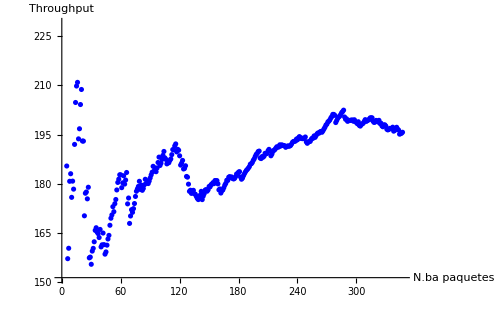
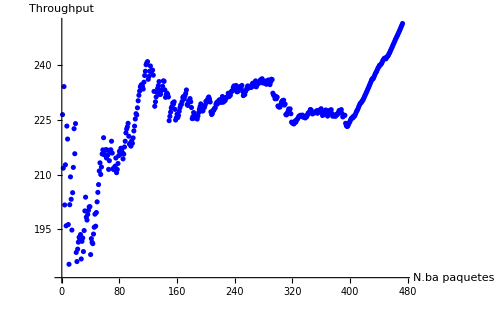
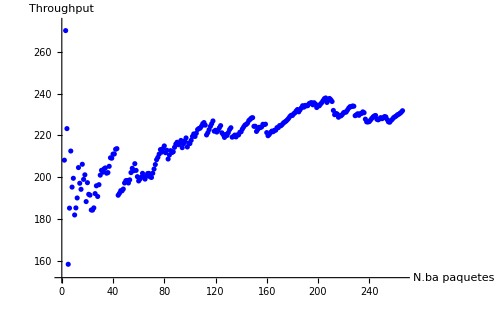
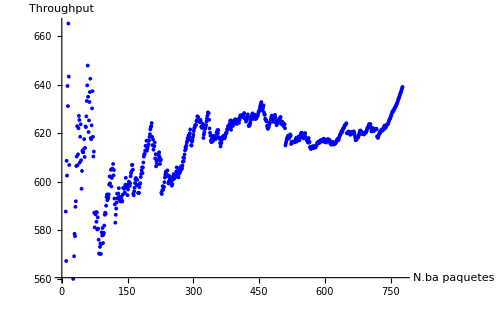
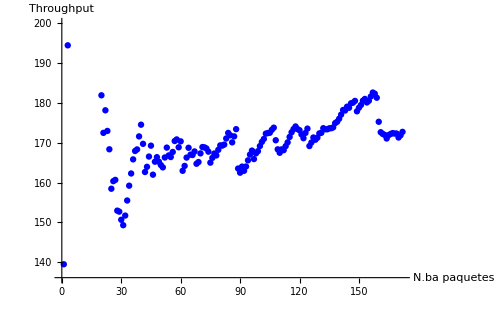
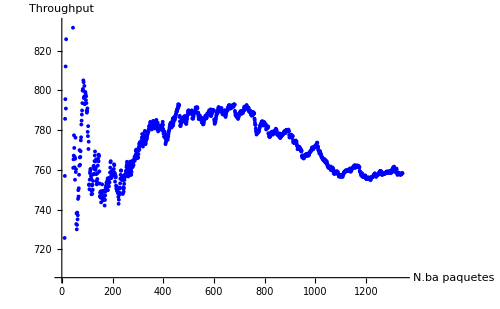
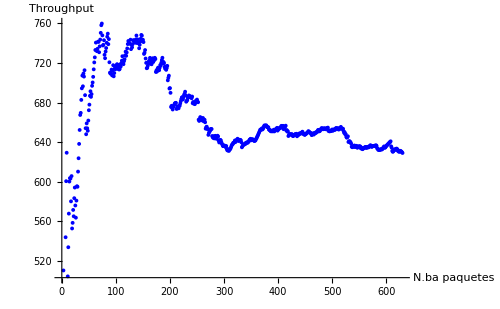
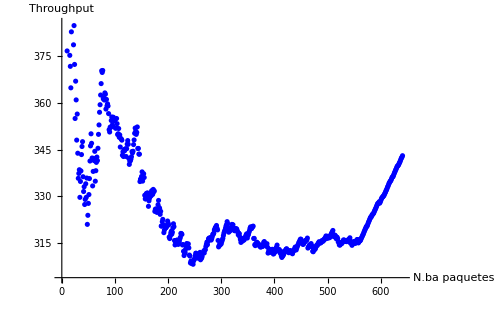
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10
```

```mathematica
ThroughputMax[paquetes123]
ThroughputMax[paquetes124]
ThroughputMax[paquetes1523]
ThroughputMax[paquetes154]
ThroughputMax[paquetes23]
ThroughputMax[paquetes24]
ThroughputMax[paquetes523]
ThroughputMax[paquetes524]
ThroughputMax[paquetes54] 
Last[paquetes123]
Last[paquetes123][[9]]
Length[paquetes123]
(Length[paquetes123]/Last[paquetes123][[1]])//N
```

195.714

172.754

251.493

639.091

758.277

629.114

343.045

281.862

889.477

{1.773,726.214,2645,0,0,2035,1,{Ori-1,2,3},1.00036}

1.00036

347

195.714

```mathematica
ThroughputMax[paquetes1524]
```

231.885

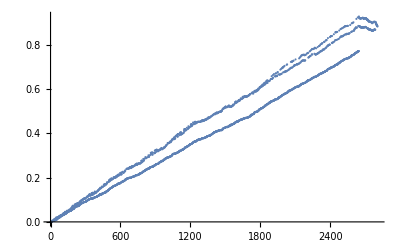

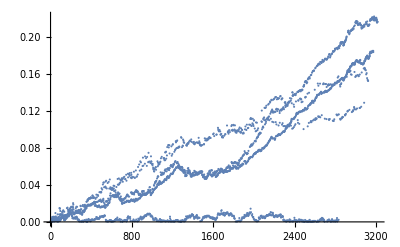

```mathematica
(*Obtencion del retardo extremo a extremo de cada paquete*)

out3;
out4;
ListPlot[Map[(#[[1]]-#[[9]])&,out3]]
ListPlot[Map[(#[[1]]-#[[9]])&,out4]]
```

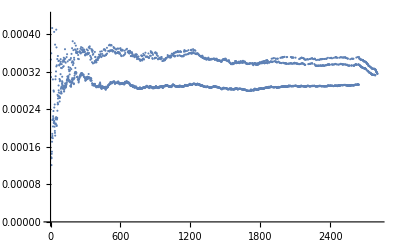

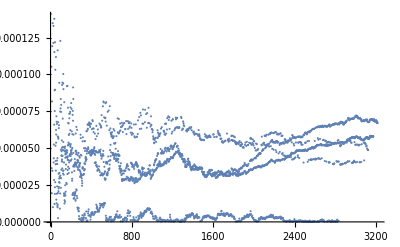

```mathematica
Module[{n=1},
ListPlot[Map[((#[[1]]-#[[9]])/n++)&,out3]]
]

Module[{n=1},
ListPlot[Map[((#[[1]]-#[[9]])/n++)&,out4]]
]
```

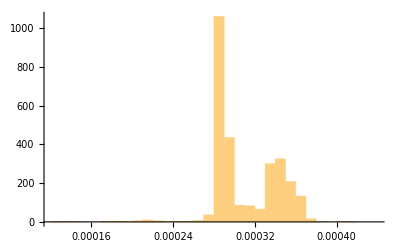

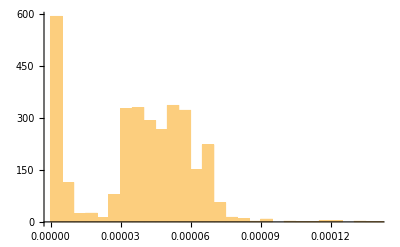

```mathematica
Module[{n=1},
Histogram[Map[((#[[1]]-#[[9]])/n++)&,out3]]
]
Module[{n=1},
Histogram[Map[((#[[1]]-#[[9]])/n++)&,out4]]
]
```

# 7B.- Obtención de estadísticas y representación gráfica de resultados parciales CON protocolo S&W

```mathematica
(*Ejecución de la función*)
opcionesDistintas3SW=ObtenerOpcionesDistintas[out3SW]
opcionesDistintas4SW=ObtenerOpcionesDistintas[out4SW]

paquetes123SW = getPacketsWithRoute[out3SW,{"Ori-1",2,3}];
paquetes1523SW = getPacketsWithRoute[out3SW,{"Ori-1",5,2,3}];
paquetes1524SW = getPacketsWithRoute[out4SW,{"Ori-1",5,2,4}];
paquetes154SW = getPacketsWithRoute[out4SW,{"Ori-1",5,4}];
paquetes124SW = getPacketsWithRoute[out4SW,{"Ori-1",2,4}]; 
paquetes23SW= getPacketsWithRoute[out3SW,{"Ori-2",2,3}];
paquetes24SW = getPacketsWithRoute[out4SW,{"Ori-2",2,4}]; 
paquetes523SW = getPacketsWithRoute[out3SW,{"Ori-5",5,2,3}];
paquetes524SW = getPacketsWithRoute[out4SW,{"Ori-5",5,2,4}]; 
paquetes54SW = getPacketsWithRoute[out4SW,{"Ori-5",5,4}]; 

tot1SW = Length[out3SW]+Length[out4SW]
tot2SW = Length[paquetes123SW]+ Length[paquetes1523SW]+Length[paquetes154SW]+Length[paquetes1524SW]+ Length[paquetes124SW]+Length[paquetes23SW]+Length[paquetes24SW]+Length[paquetes523SW]+Length[paquetes524SW]+Length[paquetes54SW]
```

{{Ori-2,2,3},{Ori-5,5,2,3},{Ori-1,2,3},{Ori-1,5,2,3}}

{{Ori-5,5,4},{Ori-2,2,4},{Ori-5,5,2,4},{Ori-1,2,4},{Ori-1,5,4},{Ori-1,5,2,4}}

5998

5998

```mathematica
t123 = getRetardo[paquetes123SW]
t124= getRetardo[paquetes124SW]
t1523 = getRetardo[paquetes1523SW]
t154 = getRetardo[paquetes154SW]
t23 = getRetardo[paquetes23SW]
t24 = getRetardo[paquetes24SW]
t523 = getRetardo[paquetes523SW]
t524 = getRetardo[paquetes524SW]
t54 = getRetardo[paquetes54SW]
```

0.0930934

0.689103

0.0575606

0.00513522

0.0556534

0.599347

0.0609868

0.603228

0.00431918

```mathematica
t1524 = getRetardo[paquetes1524SW]
```

0.655101

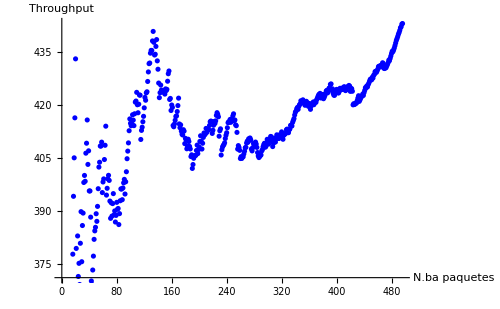
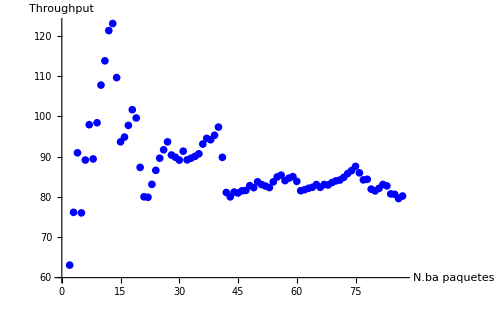
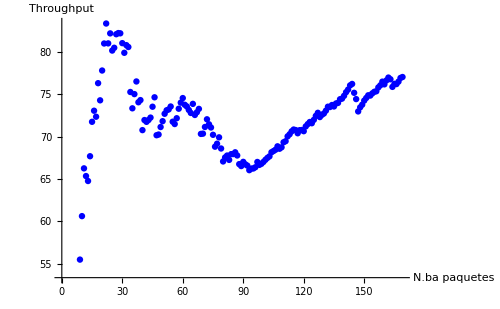
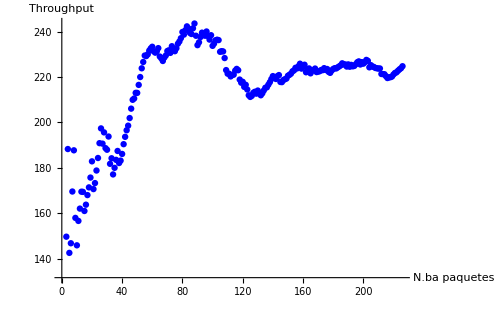
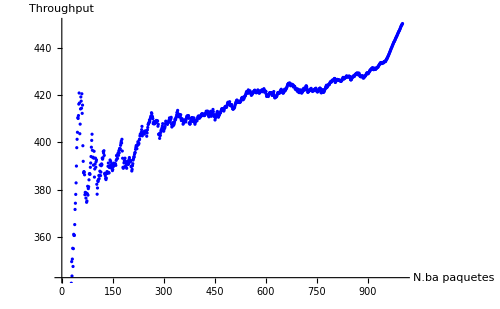
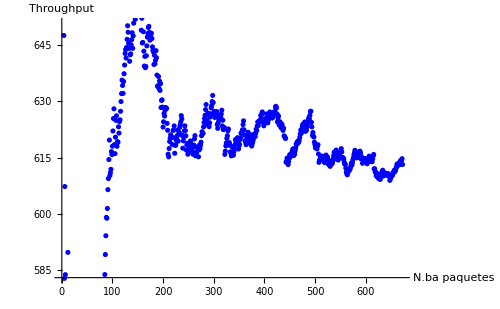
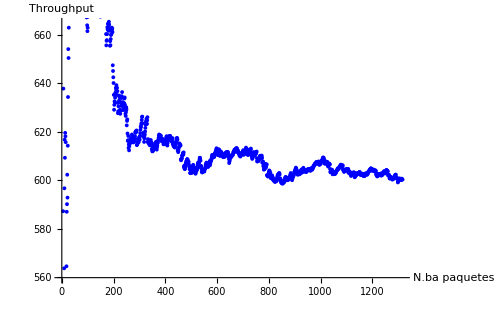
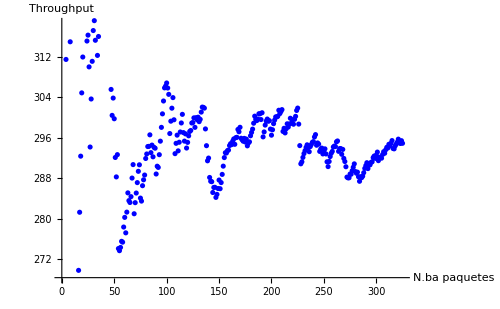
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3 | -Graphics-TH en ruta 1-5-2-4 | 
-Graphics-TH en ruta 1-5-4 | -Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3 | 
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3 | -Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10SW=Grid[{{grafica1,grafica2, grafica3},{grafica4,grafica5, grafica6},{grafica7,grafica8, grafica9, grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10SW
```

```mathematica
ThroughputMax[paquetes123SW]
ThroughputMax[paquetes124SW]
ThroughputMax[paquetes1523SW]
ThroughputMax[paquetes154SW]
ThroughputMax[paquetes23SW]
ThroughputMax[paquetes24SW]
ThroughputMax[paquetes523SW]
ThroughputMax[paquetes524SW]
ThroughputMax[paquetes54SW]
```

443.182

450.236

80.1311

224.75

613.146

600.378

294.932

308.54

1014.58

```mathematica
ThroughputMax[paquetes1524SW]
```

77.0036

{{0.00080159,1002.16,1,0,0,1,1,{Ori-2,2,3},0.000321748},{0.00163022,1584.94,2,0,0,1,1,{Ori-5,5,2,3},0.000193961},{0.00354532,973.373,3,0,0,5,1,{Ori-5,5,2,3},0.00117873},{0.00470663,418.117,4,0,0,9,1,{Ori-2,2,3},0.0044093},{0.00581126,2196.52,5,0,0,10,1,{Ori-2,2,3},0.00495818},{0.00617696,103.597,6,0,0,11,1,{Ori-2,2,3},0.00570588},{0.00729085,897.661,7,0,0,6,1,{Ori-1,2,3},0.00578377},{0.0085798,93.6161,8,0,0,18,1,{Ori-2,2,3},0.00838387},{0.00988026,159.35,9,0,0,21,1,{Ori-2,2,3},0.0096638},{0.0109872,911.763,10,0,0,8,1,{Ori-1,2,3},0.00762654}}

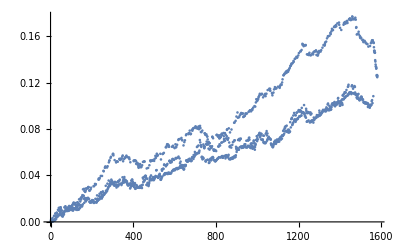

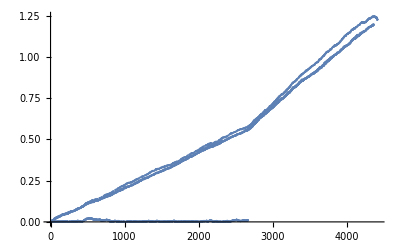

```mathematica
out3SW[[1;;10]]
out4SW;
ListPlot[Map[(#[[1]]-#[[9]])&,out3SW]]
ListPlot[Map[(#[[1]]-#[[9]])&,out4SW]]
```

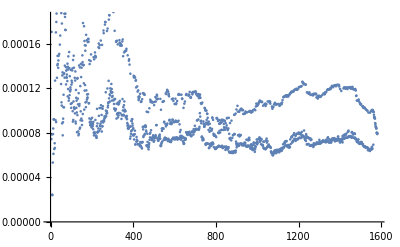

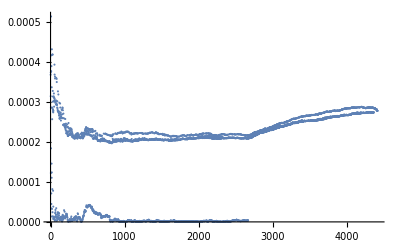

```mathematica
Module[{n=1},
ListPlot[Map[((#[[1]]-#[[9]])/n++)&,out3SW]]
]

Module[{n=1},
ListPlot[Map[((#[[1]]-#[[9]])/n++)&,out4SW]]
]
```

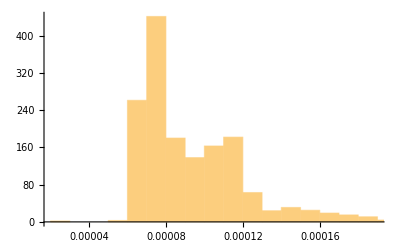

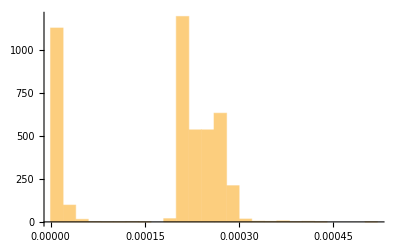

```mathematica
Module[{n=1},
Histogram[Map[((#[[1]]-#[[9]])/n++)&,out3SW]]
]
Module[{n=1},
Histogram[Map[((#[[1]]-#[[9]])/n++)&,out4SW]]
]
```

# 7C.- Obtención de estadísticas y representación gráfica de resultados parciales CON protocolo GBN

```mathematica
(*Ejecución de la función*)
opcionesDistintas3GBN=ObtenerOpcionesDistintas[out3GBN]
opcionesDistintas4GBN=ObtenerOpcionesDistintas[out4GBN]

paquetes123GBN = getPacketsWithRoute[out3GBN,{"Ori-1",2,3}];
paquetes1523GBN = getPacketsWithRoute[out3GBN,{"Ori-1",5,2,3}];
paquetes1524GBN = getPacketsWithRoute[out4GBN,{"Ori-1",5,2,4}];
paquetes154GBN = getPacketsWithRoute[out4GBN,{"Ori-1",5,4}];
paquetes124GBN = getPacketsWithRoute[out4GBN,{"Ori-1",2,4}]; 
paquetes23GBN= getPacketsWithRoute[out3GBN,{"Ori-2",2,3}];
paquetes24GBN = getPacketsWithRoute[out4GBN,{"Ori-2",2,4}]; 
paquetes523GBN = getPacketsWithRoute[out3GBN,{"Ori-5",5,2,3}];
paquetes524GBN = getPacketsWithRoute[out4GBN,{"Ori-5",5,2,4}]; 
paquetes54GBN = getPacketsWithRoute[out4GBN,{"Ori-5",5,4}]; 

tot1GBN = Length[out3GBN]+Length[out4GBN]
tot2GBN = Length[paquetes123GBN]+ Length[paquetes1523GBN]+Length[paquetes154GBN]+Length[paquetes1524GBN]+ Length[paquetes124GBN]+Length[paquetes23GBN]+Length[paquetes24GBN]+Length[paquetes523GBN]+Length[paquetes524GBN]+Length[paquetes54GBN]
```

{{Ori-5,5,2,3},{Ori-2,2,3},{Ori-1,2,3},{Ori-1,5,2,3}}

{{Ori-5,5,4},{Ori-2,2,4},{Ori-1,2,4},{Ori-1,5,4},{Ori-5,5,2,4},{Ori-1,5,2,4}}

6068

6068

```mathematica
t123 = getRetardo[paquetes123GBN]
t124= getRetardo[paquetes124GBN]
t1523 = getRetardo[paquetes1523GBN]
t154 = getRetardo[paquetes154GBN]
t23 = getRetardo[paquetes23GBN]
t24 = getRetardo[paquetes24GBN]
t523 = getRetardo[paquetes523GBN]
t524 = getRetardo[paquetes524GBN]
t54 = getRetardo[paquetes54GBN]
```

0.00212632

0.106471

0.00263291

0.00141691

0.00111585

0.108268

0.0022464

0.110353

0.00086805

```mathematica
t1524 = getRetardo[paquetes1524GBN]
```

0.104435

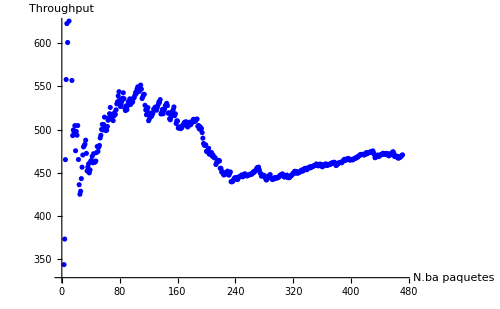
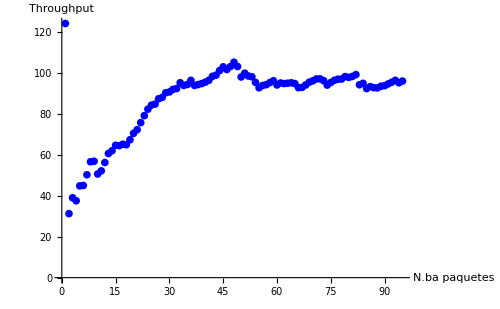
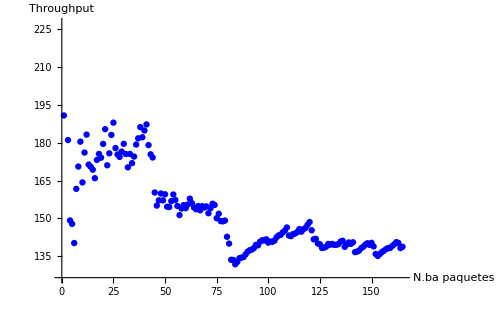
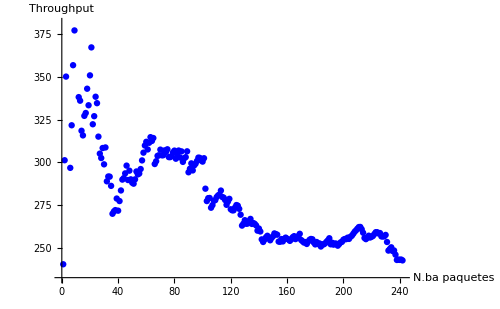
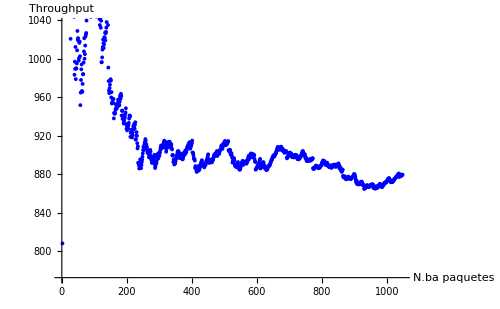
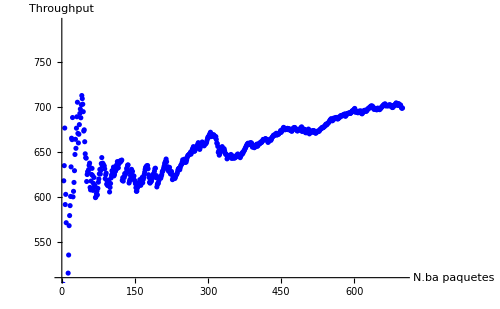
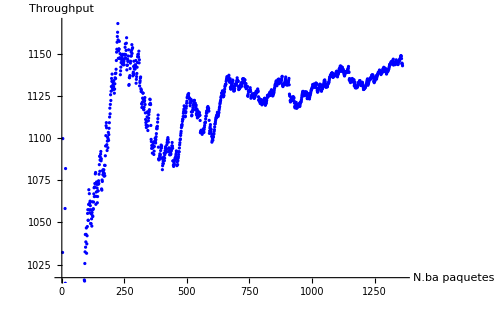
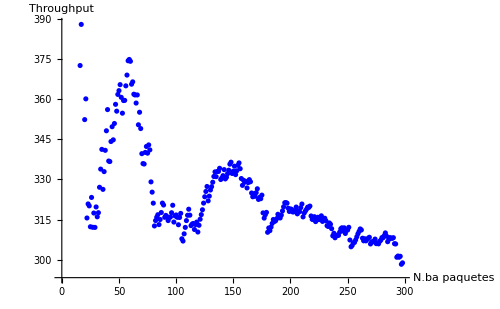
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10GBN=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10GBN
```

```mathematica
ThroughputMax[paquetes123GBN]
ThroughputMax[paquetes124GBN]
ThroughputMax[paquetes1523GBN]
ThroughputMax[paquetes154GBN]
ThroughputMax[paquetes23GBN]
ThroughputMax[paquetes24GBN]
ThroughputMax[paquetes523GBN]
ThroughputMax[paquetes524GBN]
ThroughputMax[paquetes54GBN]
```

470.822

879.134

95.9679

242.707

699.212

1142.86

298.884

576.656

1001.69

```mathematica
ThroughputMax[paquetes1524GBN]
```

138.801

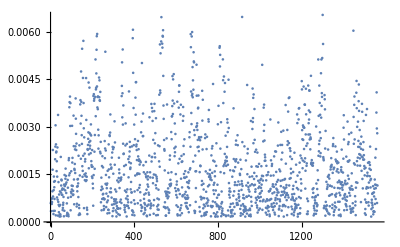

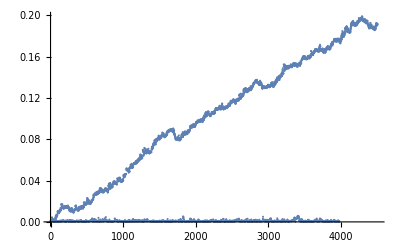

```mathematica
out3GBN[[1;;100]];
out4GBN;
ListPlot[Map[(#[[1]]-#[[9]])&,out3GBN]]
ListPlot[Map[(#[[1]]-#[[9]])&,out4GBN]]
```

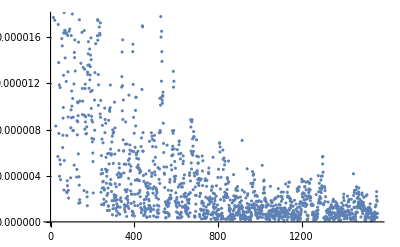

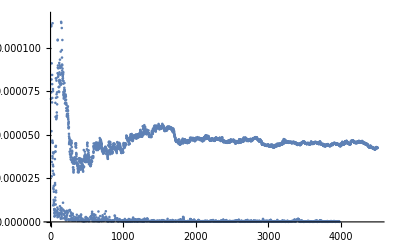

```mathematica
Module[{n=1},
ListPlot[Map[((#[[1]]-#[[9]])/n++)&,out3GBN]]
]

Module[{n=1},
ListPlot[Map[((#[[1]]-#[[9]])/n++)&,out4GBN]]
]
```

```mathematica
Module[{n=1},
Histogram[Map[((#[[1]]-#[[9]])/n++)&,out3]]
]
Module[{n=1},
Histogram[Map[((#[[1]]-#[[9]])/n++)&,out4]]
]
```

-Graphics-

-Graphics-